## Generate optimized energy, gradient, and Hessian expressions for molecular mechanics.

```mathematica
Directory[]
```

/Users/meister/Development/clasp/cando/mathematica

```mathematica
SetDirectory["/Users/meister/Development/clasp/cando/mathematica"]
```

/Users/meister/Development/clasp/cando/mathematica

## Setup to generate code that is embeded within CANDO

```mathematica
Needs["optimizeExpressions`"]
```

```mathematica
Assign[var_,exp_]:=Rule[exp,var];
```

```mathematica
(* Extract the variable name information into a list of rules *)
ExtractNames[names_] := {
	Name->names[[1]],
	XYZ->names[[2]],
	Index->names[[3]],
	Offset->names[[4]],
	Func->If[Length[names]≥5,names[[5]],0]
};
```

```mathematica
EnergyAccumulate[macroPrefix_,energyName_]:=CCode[macroPrefix<>"_ENERGY_ACCUMULATE("<>ToString[energyName]<>");"];
```

```mathematica
ForceAccumulate[macroPrefix_,nameRules_,forceName_]:= CCode[
	macroPrefix<>"_FORCE_ACCUMULATE("<>ToString[Index/.nameRules]
	<>", "<>ToString[Offset/.nameRules]<>", "<>ToString[forceName]<>" );"];
```

```mathematica
AppendGradientAndForce[macroPrefix_,be_,outputs_,rawEnergyFn_,rawNames_] := Module[
	{i,gradName,zforceName,energyFn,nameInfo,varName,names,deriv},
	PrintTemporary["About to append Gradient and Force terms"];
	names = Evaluate[rawNames];
	energyFn = Evaluate[rawEnergyFn];
	For[i=1,i≤Length[names],i++,
		nameInfo = ExtractNames[names[[i]]];
		varName = Name/.nameInfo;
		gradName = Symbol["g"<>ToString[varName]];
		zforceName = Symbol["f"<>ToString[varName]];
		deriv = D[energyFn,varName];
		PrintTemporary["Appending force term: "<>ToString[zforceName]];
		AppendTo[be,Assign[gradName,deriv]];
		AppendTo[be,Assign[zforceName,-gradName]];
		AppendTo[outputs,zforceName];
		AppendTo[be,ForceAccumulate[macroPrefix,nameInfo,zforceName]];
	];
];
SetAttributes[AppendGradientAndForce,HoldAll];
```

```mathematica
HessianAccumulate[macroPrefix_,name1Info_,name2Info_,hessianName_]:= CCode[
	macroPrefix<>"_HESSIAN_ACCUMULATE("
	<>ToString[Index/.name1Info]<>", "
	<>ToString[Offset/.name1Info]<>", "
	<>ToString[Index/.name2Info]<>", "
	<>ToString[Offset/.name2Info]<>", "
	<>ToString[hessianName]<>");"];
```

```mathematica
AppendOneHessianElement[macroPrefix_,be_,outputs_,hessianStructure_,energyFn_,names_,i_,j_]:=Module[
	{name1Info,name2Info,var1Name,var2Name,hessianName,hess,prefix,zfirstDeriv},
	name1Info = ExtractNames[names[[i]]];
	name2Info = ExtractNames[names[[j]]];
	var1Name = Name/.name1Info;
	var2Name = Name/.name2Info;
	If[i==j,prefix="d"(*Diagonal*),prefix="o"];
	hessianName = Symbol[prefix<>"h"<>ToString[var1Name]<>ToString[var2Name]];
	zfirstDeriv = D[energyFn,var1Name];
	hess = D[zfirstDeriv,var2Name];
	AppendTo[be,Assign[hessianName,hess]];
	AppendTo[outputs,hessianName];
	AppendTo[be,HessianAccumulate[macroPrefix,name1Info,name2Info,hessianName]];
	PrintTemporary["Appended hessian element ("<>ToString[j]
				<>","<>ToString[i]<>") for variable: "<>ToString[hessianName]];
	hessianStructure[[i,j]]=Length[outputs];
	If[i≠j,hessianStructure[[j,i]]=Length[outputs]];
];
SetAttributes[AppendOneHessianElement,HoldAll];
```

```mathematica
AppendHessianDiagonalElements[macroPrefix_,be_,outputs_,hessianStructure_,rawEnergyFn_,rawNames_] := Module[
	{names,energyFn,i},
	names = Evaluate[rawNames];
	energyFn = Evaluate[rawEnergyFn];
	For[i=1,i≤Length[names],i++,
		AppendOneHessianElement[macroPrefix<>"_DIAGONAL",be,outputs,hessianStructure,energyFn,names,i,i];
	];
];
SetAttributes[AppendHessianDiagonalElements,HoldAll];
```

```mathematica
AppendHessianOffDiagonalElements[macroPrefix_,be_,outputs_,hessianStructure_,rawEnergyFn_,rawNames_] := Module[
	{energyFn,name1Info,name2Info,var1Name,var2Name,hessianName,col,row,names},
	names = Evaluate[rawNames];
	energyFn = Evaluate[rawEnergyFn];
	For[col=1,col<Length[names],col++,
		For[row=col+1,row<=Length[names],row++,
			AppendOneHessianElement[macroPrefix<>"_OFF_DIAGONAL",be,outputs,hessianStructure,energyFn,names,col,row];
		];
	];
];
SetAttributes[AppendHessianOffDiagonalElements,HoldAll];
```

```mathematica
(* Now do everything *)
AppendGradientForceAndHessian[macroPrefix_,be_,outputs_,hessianStructure_,rawEnergyFn_,rawVarNames_]:= Module[
	{energyFn,varNames},
	energyFn = Evaluate[rawEnergyFn];
	varNames = Evaluate[rawVarNames];
	AppendTo[be,CCode["#ifdef "<>macroPrefix<>"_CALC_FORCE //["]];
	AppendTo[be,CCode["if ( calcForce ) {"] ];
	AppendGradientAndForce[macroPrefix,be,outputs,energyFn,varNames];
	AppendTo[be,CCode["#ifdef "<>macroPrefix<>"_CALC_DIAGONAL_HESSIAN //["]];
	AppendTo[be,CCode["if ( calcDiagonalHessian ) {"]];
	AppendHessianDiagonalElements[macroPrefix,be,outputs,hessianStructure,energyFn,varNames];
	AppendTo[be,CCode["#ifdef "<>macroPrefix<>"_CALC_OFF_DIAGONAL_HESSIAN //["]];
	AppendTo[be, CCode["if ( calcOffDiagonalHessian ) {" ]];
	AppendHessianOffDiagonalElements[macroPrefix, be, outputs,hessianStructure, energyFn, varNames];
	AppendTo[be, CCode["} /*if calcOffDiagonalHessian */ "]];
	AppendTo[be, CCode["#endif /* "<>macroPrefix<>"_CALC_OFF_DIAGONAL_HESSIAN ]*/"]];
	AppendTo[be,CCode["} /*calcDiagonalHessian */"]];
	AppendTo[be, CCode["#endif /* "<>macroPrefix<>"_CALC_DIAGONAL_HESSIAN ]*/"]];
	AppendTo[be,CCode["} /*calcForce */"]];
	AppendTo[be, CCode["#endif /* "<>macroPrefix<>"_CALC_FORCE ]*/"]];
];
SetAttributes[AppendGradientForceAndHessian,HoldAll];
```

## Bond stretch term between two atoms with coordinates {x1,y1,z1} and {x2,y2,z2} - Expand the gradient and Hessian.

```mathematica
Clear[x1,y1,z1,x2,y2,z2];
```

```mathematica
ba = { x1, y1, z1};
bb = { x2, y2, z2 };
```

### Define the Hooks law bond stretch potential

```mathematica
stretchDeviation = Sqrt[(bb-ba).(bb-ba)]-r0;
```

```mathematica
stretchEnergyFn =  kb  (stretchDeviation)^2.0
```

kb (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^2.

```mathematica
names = Flatten[{ba,bb}]
```

{x1,y1,z1,x2,y2,z2}

### Assemble the energy function rules to expand

```mathematica
stretchVarNames = { 
{x1,x,I1,0},
{y1,y,I1,1},
{z1,z,I1,2},
{x2,x,I2,0},
{y2,y,I2,1},
{z2,z,I2,2}
};
```

```mathematica
stretchSetupRules = {};
AppendTo[stretchSetupRules,CCode["STRETCH_SET_PARAMETER(kb);"]];
AppendTo[stretchSetupRules,CCode["STRETCH_SET_PARAMETER(r0);"]];
AppendTo[stretchSetupRules,CCode["STRETCH_SET_PARAMETER(I1);"]];
AppendTo[stretchSetupRules,CCode["STRETCH_SET_PARAMETER(I2);"]];
```

```mathematica
For[i=1,i≤Length[stretchVarNames],i++,
str = "STRETCH_SET_POSITION("<>ToString[stretchVarNames[[i]][[1]]]<>","<>ToString[stretchVarNames[[i]][[3]]]<>","<>ToString[stretchVarNames[[i]][[4]]]<>");";
Print[str];
AppendTo[stretchSetupRules,CCode[str]];
];
```

STRETCH_SET_POSITION(x1,I1,0);

STRETCH_SET_POSITION(y1,I1,1);

STRETCH_SET_POSITION(z1,I1,2);

STRETCH_SET_POSITION(x2,I2,0);

STRETCH_SET_POSITION(y2,I2,1);

STRETCH_SET_POSITION(z2,I2,2);

```mathematica
stretchSetupRules//MatrixForm
```

(CCode[STRETCH_SET_PARAMETER(kb);]
CCode[STRETCH_SET_PARAMETER(r0);]
CCode[STRETCH_SET_PARAMETER(I1);]
CCode[STRETCH_SET_PARAMETER(I2);]
CCode[STRETCH_SET_POSITION(x1,I1,0);]
CCode[STRETCH_SET_POSITION(y1,I1,1);]
CCode[STRETCH_SET_POSITION(z1,I1,2);]
CCode[STRETCH_SET_POSITION(x2,I2,0);]
CCode[STRETCH_SET_POSITION(y2,I2,1);]
CCode[STRETCH_SET_POSITION(z2,I2,2);])

```mathematica
stretchEnergyRules = {};
stretchOutputs = {};
AppendTo[stretchEnergyRules,Assign[StretchDeviation,stretchDeviation]];
AppendTo[stretchEnergyRules,Assign[Energy,stretchEnergyFn]];
AppendTo[stretchEnergyRules,EnergyAccumulate["STRETCH",Energy]];
AppendTo[stretchOutputs,Energy];
```

### Append the Gradient and Hessian rules

```mathematica
stretchEnergyFn
```

kb (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^2.

```mathematica
(stretchHessian = Table[Table[0,{6}],{6}])//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
stretchForceHessianRules = {};
```

```mathematica
AppendGradientForceAndHessian["STRETCH",stretchForceHessianRules,stretchOutputs,stretchHessian,stretchEnergyFn,stretchVarNames];
```

```mathematica
stretchHessian//MatrixForm
```

(8 | 14 | 15 | 16 | 17 | 18
14 | 9 | 19 | 20 | 21 | 22
15 | 19 | 10 | 23 | 24 | 25
16 | 20 | 23 | 11 | 26 | 27
17 | 21 | 24 | 26 | 12 | 28
18 | 22 | 25 | 27 | 28 | 13)

```mathematica
stretchOutputs
```

{Energy,fx1,fy1,fz1,fx2,fy2,fz2,dhx1x1,dhy1y1,dhz1z1,dhx2x2,dhy2y2,dhz2z2,ohx1y1,ohx1z1,ohx1x2,ohx1y2,ohx1z2,ohy1z1,ohy1x2,ohy1y2,ohy1z2,ohz1x2,ohz1y2,ohz1z2,ohx2y2,ohx2z2,ohy2z2}

### Collect terms and convert to C code

```mathematica
stretchAllRules ={
stretchSetupRules,
stretchEnergyRules,
stretchForceHessianRules};
```

```mathematica
stretchRules = Flatten[stretchAllRules];
```

```mathematica
stretchRules
```

{CCode[STRETCH_SET_PARAMETER(kb);],CCode[STRETCH_SET_PARAMETER(r0);],CCode[STRETCH_SET_PARAMETER(I1);],CCode[STRETCH_SET_PARAMETER(I2);],CCode[STRETCH_SET_POSITION(x1,I1,0);],CCode[STRETCH_SET_POSITION(y1,I1,1);],CCode[STRETCH_SET_POSITION(z1,I1,2);],CCode[STRETCH_SET_POSITION(x2,I2,0);],CCode[STRETCH_SET_POSITION(y2,I2,1);],CCode[STRETCH_SET_POSITION(z2,I2,2);],-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)→StretchDeviation,kb (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^2.→Energy,CCode[STRETCH_ENERGY_ACCUMULATE(Energy);],CCode[#ifdef STRETCH_CALC_FORCE //[],CCode[if ( calcForce ) {],-(2. kb (-x1+x2) (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))→gx1,-gx1→fx1,CCode[STRETCH_FORCE_ACCUMULATE(I1, 0, fx1 );],-(2. kb (-y1+y2) (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))→gy1,-gy1→fy1,CCode[STRETCH_FORCE_ACCUMULATE(I1, 1, fy1 );],-(2. kb (-z1+z2) (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))→gz1,-gz1→fz1,CCode[STRETCH_FORCE_ACCUMULATE(I1, 2, fz1 );],(2. kb (-x1+x2) (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))→gx2,-gx2→fx2,CCode[STRETCH_FORCE_ACCUMULATE(I2, 0, fx2 );],(2. kb (-y1+y2) (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))→gy2,-gy2→fy2,CCode[STRETCH_FORCE_ACCUMULATE(I2, 1, fy2 );],(2. kb (-z1+z2) (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))→gz2,-gz2→fz2,CCode[STRETCH_FORCE_ACCUMULATE(I2, 2, fz2 );],CCode[#ifdef STRETCH_CALC_DIAGONAL_HESSIAN //[],CCode[if ( calcDiagonalHessian ) {],(2. kb (-x1+x2)^2)/((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)-(2. kb (-x1+x2)^2 (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))+(2. kb (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))→dhx1x1,CCode[STRETCH_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 0, dhx1x1);],(2. kb (-y1+y2)^2)/((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)-(2. kb (-y1+y2)^2 (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))+(2. kb (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))→dhy1y1,CCode[STRETCH_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 1, dhy1y1);],(2. kb (-z1+z2)^2)/((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)-(2. kb (-z1+z2)^2 (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))+(2. kb (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))→dhz1z1,CCode[STRETCH_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I1, 2, dhz1z1);],(2. kb (-x1+x2)^2)/((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)-(2. kb (-x1+x2)^2 (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))+(2. kb (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))→dhx2x2,CCode[STRETCH_DIAGONAL_HESSIAN_ACCUMULATE(I2, 0, I2, 0, dhx2x2);],(2. kb (-y1+y2)^2)/((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)-(2. kb (-y1+y2)^2 (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))+(2. kb (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))→dhy2y2,CCode[STRETCH_DIAGONAL_HESSIAN_ACCUMULATE(I2, 1, I2, 1, dhy2y2);],(2. kb (-z1+z2)^2)/((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)-(2. kb (-z1+z2)^2 (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))+(2. kb (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))→dhz2z2,CCode[STRETCH_DIAGONAL_HESSIAN_ACCUMULATE(I2, 2, I2, 2, dhz2z2);],CCode[#ifdef STRETCH_CALC_OFF_DIAGONAL_HESSIAN //[],CCode[if ( calcOffDiagonalHessian ) {],(2. kb (-x1+x2) (-y1+y2))/((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)-(2. kb (-x1+x2) (-y1+y2) (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))→ohx1y1,CCode[STRETCH_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 1, ohx1y1);],(2. kb (-x1+x2) (-z1+z2))/((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)-(2. kb (-x1+x2) (-z1+z2) (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))→ohx1z1,CCode[STRETCH_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 2, ohx1z1);],-(2. kb (-x1+x2)^2)/((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)+(2. kb (-x1+x2)^2 (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))-(2. kb (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))→ohx1x2,CCode[STRETCH_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I2, 0, ohx1x2);],-(2. kb (-x1+x2) (-y1+y2))/((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)+(2. kb (-x1+x2) (-y1+y2) (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))→ohx1y2,CCode[STRETCH_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I2, 1, ohx1y2);],-(2. kb (-x1+x2) (-z1+z2))/((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)+(2. kb (-x1+x2) (-z1+z2) (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))→ohx1z2,CCode[STRETCH_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I2, 2, ohx1z2);],(2. kb (-y1+y2) (-z1+z2))/((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)-(2. kb (-y1+y2) (-z1+z2) (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))→ohy1z1,CCode[STRETCH_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 2, ohy1z1);],-(2. kb (-x1+x2) (-y1+y2))/((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)+(2. kb (-x1+x2) (-y1+y2) (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))→ohy1x2,CCode[STRETCH_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I2, 0, ohy1x2);],-(2. kb (-y1+y2)^2)/((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)+(2. kb (-y1+y2)^2 (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))-(2. kb (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))→ohy1y2,CCode[STRETCH_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I2, 1, ohy1y2);],-(2. kb (-y1+y2) (-z1+z2))/((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)+(2. kb (-y1+y2) (-z1+z2) (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))→ohy1z2,CCode[STRETCH_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I2, 2, ohy1z2);],-(2. kb (-x1+x2) (-z1+z2))/((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)+(2. kb (-x1+x2) (-z1+z2) (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))→ohz1x2,CCode[STRETCH_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I2, 0, ohz1x2);],-(2. kb (-y1+y2) (-z1+z2))/((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)+(2. kb (-y1+y2) (-z1+z2) (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))→ohz1y2,CCode[STRETCH_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I2, 1, ohz1y2);],-(2. kb (-z1+z2)^2)/((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)+(2. kb (-z1+z2)^2 (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))-(2. kb (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))→ohz1z2,CCode[STRETCH_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I2, 2, ohz1z2);],(2. kb (-x1+x2) (-y1+y2))/((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)-(2. kb (-x1+x2) (-y1+y2) (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))→ohx2y2,CCode[STRETCH_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I2, 0, I2, 1, ohx2y2);],(2. kb (-x1+x2) (-z1+z2))/((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)-(2. kb (-x1+x2) (-z1+z2) (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))→ohx2z2,CCode[STRETCH_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I2, 0, I2, 2, ohx2z2);],(2. kb (-y1+y2) (-z1+z2))/((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)-(2. kb (-y1+y2) (-z1+z2) (-r0+√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2))^1.)/(((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))→ohy2z2,CCode[STRETCH_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I2, 1, I2, 2, ohy2z2);],CCode[} /*if calcOffDiagonalHessian */ ],CCode[#endif /* STRETCH_CALC_OFF_DIAGONAL_HESSIAN ]*/],CCode[} /*calcDiagonalHessian */],CCode[#endif /* STRETCH_CALC_DIAGONAL_HESSIAN ]*/],CCode[} /*calcForce */],CCode[#endif /* STRETCH_CALC_FORCE ]*/]}

```mathematica
stretchInput = {x1,y1,z1,x2,y2,z2,r0,kb};
```

```mathematica
AppendTo[stretchOutputs,StretchDeviation];
```

### Assemble the rules, the name of the energy term, the independant variable names, etc. into what passes for a structure in Mathematica (I call it a Pack)

```mathematica
stretchPack0 = {
Name->"Stretch",
AdditionalCDeclares->"",
DerivativeVariables->{x1,y1,z1,x2,y2,z2},
HessianStructure->stretchHessian,
Rules->stretchRules,
Input->stretchInput,
Output->stretchOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[stretchPack0];
```

Writing finite difference debug code to: _Stretch_debugFiniteDifference.cc

Writing debug variable declares to: _Stretch_debugEvalDeclares.cc

Writing xml output debug code to: _Stretch_debugEvalSerialize.cc

Writing set variables debug code to: _Stretch_debugEvalSet.cc

stretchPack = Block[{PrintTemporary = Print}, packOptimize[stretchPack0]];

### Put the pedal to the metal and generate "C" code.

```mathematica
stretchPack = packOptimize[stretchPack0];
```

Set TimesSimplify and PlusSimplify to turn these simplifications off and on

PlusOptimize = True

TimesOptimize = True

Writing declares to file: _Stretch_termDeclares.cc

Writing code to file: _Stretch_termCode.cc

### Draw an evaluation tree for the optimized "C" code. It doesn' t do anything useful but it looks impressive - I have got to print some of these on large format posters. Inputs (independent variables and parameters) are on the left and drawn in Black, and outputs are on the right and also drawn in Black. Computationally expensive functions are highlighted in red, Plus functions are blue and Times functions are green.

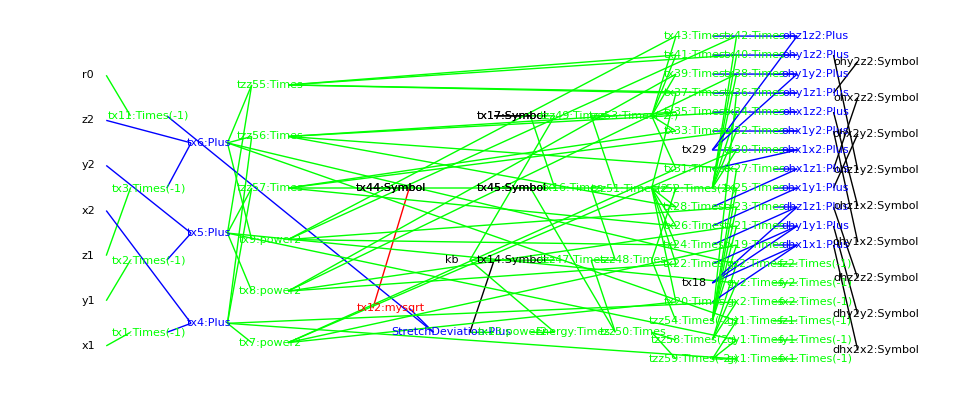

```mathematica
packGraph[stretchPack]
```

## Angle bend term using Mathematica generated gradient/Hessian expansion

```mathematica
Clear[x1,y1,z1,x2,y2,z2,x3,y3,z3,ab,cb,ba,bb,bc];
```

```mathematica
ba = { x1, y1, z1};
bb = { x2, y2, z2 };
bc = { x3, y3, z3 };
```

```mathematica
angleInputs = Flatten[{ba,bb,bc,{t0,kt}}]
```

{x1,y1,z1,x2,y2,z2,x3,y3,z3,t0,kt}

```mathematica
vecLen[a_] := Sqrt[Dot[a,a]];
```

```mathematica
ab= ba - bb;
cb = bc - bb;
dotNormAbNormCb= Dot[ab,cb]/(vecLen[ab]vecLen[cb]);
fnThetaDev = ArcCos[dotNormAbNormCb]-t0
```

-t0+ArcCos[((x1-x2) (-x2+x3)+(y1-y2) (-y2+y3)+(z1-z2) (-z2+z3))/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2) √((-x2+x3)^2+(-y2+y3)^2+(-z2+z3)^2))]

```mathematica
angleEnergyFn =  kt (thetaDev)^2
```

kt thetaDev^2

```mathematica
angleEnergyFn = angleEnergyFn/.{thetaDev->fnThetaDev}
```

kt (-t0+ArcCos[((x1-x2) (-x2+x3)+(y1-y2) (-y2+y3)+(z1-z2) (-z2+z3))/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2) √((-x2+x3)^2+(-y2+y3)^2+(-z2+z3)^2))])^2

```mathematica
names = Flatten[{ba,bb,bc}]
```

{x1,y1,z1,x2,y2,z2,x3,y3,z3}

### Energy

```mathematica
angleVarNames = { 
{x1,x,I1,0},
{y1,y,I1,1},
{z1,z,I1,2},
{x2,x,I2,0},
{y2,y,I2,1},
{z2,z,I2,2},
{x3,x,I3,0},
{y3,y,I3,1},
{z3,z,I3,2}
};
```

```mathematica
angleSetupRules = {};
AppendTo[angleSetupRules,CCode["ANGLE_SET_PARAMETER(kt);"]];
AppendTo[angleSetupRules,CCode["ANGLE_SET_PARAMETER(t0);"]];
AppendTo[angleSetupRules,CCode["ANGLE_SET_PARAMETER(I1);"]];
AppendTo[angleSetupRules,CCode["ANGLE_SET_PARAMETER(I2);"]];
AppendTo[angleSetupRules,CCode["ANGLE_SET_PARAMETER(I3);"]];
```

```mathematica
For[i=1,i≤Length[angleVarNames],i++,
str = "ANGLE_SET_POSITION("<>ToString[angleVarNames[[i]][[1]]]<>","<>ToString[angleVarNames[[i]][[3]]]<>","<>ToString[angleVarNames[[i]][[4]]]<>");";
Print[str];
AppendTo[angleSetupRules,CCode[str]];
];
```

ANGLE_SET_POSITION(x1,I1,0);

ANGLE_SET_POSITION(y1,I1,1);

ANGLE_SET_POSITION(z1,I1,2);

ANGLE_SET_POSITION(x2,I2,0);

ANGLE_SET_POSITION(y2,I2,1);

ANGLE_SET_POSITION(z2,I2,2);

ANGLE_SET_POSITION(x3,I3,0);

ANGLE_SET_POSITION(y3,I3,1);

ANGLE_SET_POSITION(z3,I3,2);

```mathematica
angleSetupRules//MatrixForm
```

(CCode[ANGLE_SET_PARAMETER(kt);]
CCode[ANGLE_SET_PARAMETER(t0);]
CCode[ANGLE_SET_PARAMETER(I1);]
CCode[ANGLE_SET_PARAMETER(I2);]
CCode[ANGLE_SET_PARAMETER(I3);]
CCode[ANGLE_SET_POSITION(x1,I1,0);]
CCode[ANGLE_SET_POSITION(y1,I1,1);]
CCode[ANGLE_SET_POSITION(z1,I1,2);]
CCode[ANGLE_SET_POSITION(x2,I2,0);]
CCode[ANGLE_SET_POSITION(y2,I2,1);]
CCode[ANGLE_SET_POSITION(z2,I2,2);]
CCode[ANGLE_SET_POSITION(x3,I3,0);]
CCode[ANGLE_SET_POSITION(y3,I3,1);]
CCode[ANGLE_SET_POSITION(z3,I3,2);])

```mathematica
angleOutputs = {};
```

```mathematica
angleHessian = Table[Table[0,{9}],{9}]
```

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

```mathematica
angleEnergyRules = {};
AppendTo[angleEnergyRules,Assign[DotNormAbNormCb,dotNormAbNormCb]];
AppendTo[angleEnergyRules,Assign[AngleDeviation,fnThetaDev]];
AppendTo[angleEnergyRules,CCode["bool IllegalAngle=false;"]];
AppendTo[angleEnergyRules,CCode["if(fabs(DotNormAbNormCb)>(1.0-VERYSMALL)) IllegalAngle=true;"]];
AppendTo[angleEnergyRules,Assign[Energy,angleEnergyFn]];
AppendTo[angleEnergyRules,EnergyAccumulate["ANGLE",Energy]];
AppendTo[angleOutputs,Energy];
```

```mathematica
angleForceHessianRules = {};
AppendGradientForceAndHessian["ANGLE",angleForceHessianRules,angleOutputs,angleHessian,angleEnergyFn,angleVarNames];
```

### Collect and simplify

```mathematica
Length[angleEnergyRules]
```

6

```mathematica
angleRules = Flatten[{angleSetupRules,angleEnergyRules,angleForceHessianRules}];
```

```mathematica
AppendTo[angleOutputs,AngleDeviation];
```

```mathematica
angleOutputs//FullForm
```

List[Energy,fx1,fy1,fz1,fx2,fy2,fz2,fx3,fy3,fz3,dhx1x1,dhy1y1,dhz1z1,dhx2x2,dhy2y2,dhz2z2,dhx3x3,dhy3y3,dhz3z3,ohx1y1,ohx1z1,ohx1x2,ohx1y2,ohx1z2,ohx1x3,ohx1y3,ohx1z3,ohy1z1,ohy1x2,ohy1y2,ohy1z2,ohy1x3,ohy1y3,ohy1z3,ohz1x2,ohz1y2,ohz1z2,ohz1x3,ohz1y3,ohz1z3,ohx2y2,ohx2z2,ohx2x3,ohx2y3,ohx2z3,ohy2z2,ohy2x3,ohy2y3,ohy2z3,ohz2x3,ohz2y3,ohz2z3,ohx3y3,ohx3z3,ohy3z3,AngleDeviation]

```mathematica
anglePack0 = {
Name->"Angle",
AdditionalCDeclares->"",
EnergyFunction->angleEnergyFn,
DerivativeVariables->{x1,y1,z1,x2,y2,z2,x3,y3,z3},
HessianStructure -> angleHessian,
Rules->angleRules,
Input->angleInputs,
Output->angleOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[anglePack0];
```

Writing finite difference debug code to: _Angle_debugFiniteDifference.cc

Writing debug variable declares to: _Angle_debugEvalDeclares.cc

Writing xml output debug code to: _Angle_debugEvalSerialize.cc

Writing set variables debug code to: _Angle_debugEvalSet.cc

```mathematica
anglePack = packOptimize[anglePack0];
```

Set TimesSimplify and PlusSimplify to turn these simplifications off and on

PlusOptimize = True

TimesOptimize = True

Writing declares to file: _Angle_termDeclares.cc

Writing code to file: _Angle_termCode.cc

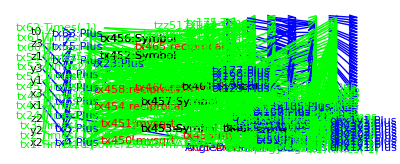

```mathematica
packGraph[anglePack]
```

## Non-bonding terms - Van der Waals and Electrostatic interactions. - Expand the gradient and Hessian in the most straightforward, simple-minded way, don't use the chain rule approach.

```mathematica
Clear[x1,y1,z1,x2,y2,z2, evdw, eeel,nonbondEquation];
```

```mathematica
ba = { x1, y1, z1};
bb = { x2, y2, z2 };
```

```mathematica
nonBondInputs = Flatten[{ba,bb,dA,dC,dQ1Q2}]
```

{x1,y1,z1,x2,y2,z2,dA,dC,dQ1Q2}

```mathematica
nonbondDistance = Sqrt[Dot[(ba-bb),(ba-bb)]];
```

```mathematica
evdwEquation = (dA/nonbondDistance^12-dC/nonbondDistance^6)
```

dA/(((x1-x2)^2+(y1-y2)^2+(z1-z2)^2)^6)-dC/(((x1-x2)^2+(y1-y2)^2+(z1-z2)^2)^3)

```mathematica
eeelEquation = (dQ1Q2/nonbondDistance)
```

dQ1Q2/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))

```mathematica
nonbondEquation = evdwEquation + eeelEquation
```

dA/(((x1-x2)^2+(y1-y2)^2+(z1-z2)^2)^6)-dC/(((x1-x2)^2+(y1-y2)^2+(z1-z2)^2)^3)+dQ1Q2/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))

```mathematica
names = Flatten[{ba,bb}]
```

{x1,y1,z1,x2,y2,z2}

### Energy

```mathematica
nonbondVarNames = { 
{x1,x,I1,0},
{y1,y,I1,1},
{z1,z,I1,2},
{x2,x,I2,0},
{y2,y,I2,1},
{z2,z,I2,2}
};
```

```mathematica
nonbondSetupRules = {};
AppendTo[nonbondSetupRules,CCode["NONBOND_SET_PARAMETER(I1);"]];
AppendTo[nonbondSetupRules,CCode["NONBOND_SET_PARAMETER(I2);"]];AppendTo[nonbondSetupRules,CCode["NONBOND_SET_PARAMETER(dQ1Q2);"]];AppendTo[nonbondSetupRules,CCode["NONBOND_SET_PARAMETER(dA);"]];
AppendTo[nonbondSetupRules,CCode["NONBOND_SET_PARAMETER(dC);"]];
```

```mathematica
For[i=1,i≤Length[nonbondVarNames],i++,
str = "NONBOND_SET_POSITION("<>ToString[nonbondVarNames[[i]][[1]]]<>","<>ToString[nonbondVarNames[[i]][[3]]]<>","<>ToString[nonbondVarNames[[i]][[4]]]<>");";
Print[str];
AppendTo[nonbondSetupRules,CCode[str]];
];
```

NONBOND_SET_POSITION(x1,I1,0);

NONBOND_SET_POSITION(y1,I1,1);

NONBOND_SET_POSITION(z1,I1,2);

NONBOND_SET_POSITION(x2,I2,0);

NONBOND_SET_POSITION(y2,I2,1);

NONBOND_SET_POSITION(z2,I2,2);

```mathematica
nonbondSetupRules//MatrixForm
```

(CCode[NONBOND_SET_PARAMETER(I1);]
CCode[NONBOND_SET_PARAMETER(I2);]
CCode[NONBOND_SET_PARAMETER(dQ1Q2);]
CCode[NONBOND_SET_PARAMETER(dA);]
CCode[NONBOND_SET_PARAMETER(dC);]
CCode[NONBOND_SET_POSITION(x1,I1,0);]
CCode[NONBOND_SET_POSITION(y1,I1,1);]
CCode[NONBOND_SET_POSITION(z1,I1,2);]
CCode[NONBOND_SET_POSITION(x2,I2,0);]
CCode[NONBOND_SET_POSITION(y2,I2,1);]
CCode[NONBOND_SET_POSITION(z2,I2,2);])

```mathematica
nonbondEnergyRules = {};
nonbondOutputs = {};
AppendTo[nonbondEnergyRules,Assign[NonbondDistance,nonbondDistance]];
AppendTo[nonbondEnergyRules,Assign[Evdw,evdwEquation]];
AppendTo[nonbondEnergyRules,EnergyAccumulate["NONBOND_EVDW",Evdw]];
AppendTo[nonbondEnergyRules,Assign[Eeel,eeelEquation]];
AppendTo[nonbondEnergyRules,EnergyAccumulate["NONBOND_EEEL",Eeel]];
AppendTo[nonbondEnergyRules,Assign[Energy,Evdw+Eeel]];
AppendTo[nonbondEnergyRules,EnergyAccumulate["NONBOND",Energy]];
AppendTo[nonbondOutputs,Energy];
AppendTo[nonbondOutputs,Evdw];
AppendTo[nonbondOutputs,Eeel];
```

```mathematica
nonbondHessian = Table[Table[0,{6}],{6}]
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
nonbondForceHessianRules = {};
```

```mathematica
AppendGradientForceAndHessian["NONBOND",nonbondForceHessianRules,nonbondOutputs,nonbondHessian,nonbondEquation,nonbondVarNames];
```

### Collect and simplify.

```mathematica
AppendTo[nonbondOutputs,NonbondDistance]
```

{Energy,Evdw,Eeel,fx1,fy1,fz1,fx2,fy2,fz2,dhx1x1,dhy1y1,dhz1z1,dhx2x2,dhy2y2,dhz2z2,ohx1y1,ohx1z1,ohx1x2,ohx1y2,ohx1z2,ohy1z1,ohy1x2,ohy1y2,ohy1z2,ohz1x2,ohz1y2,ohz1z2,ohx2y2,ohx2z2,ohy2z2,NonbondDistance}

```mathematica
nonbondOutputs//FullForm
```

List[Energy,Evdw,Eeel,fx1,fy1,fz1,fx2,fy2,fz2,dhx1x1,dhy1y1,dhz1z1,dhx2x2,dhy2y2,dhz2z2,ohx1y1,ohx1z1,ohx1x2,ohx1y2,ohx1z2,ohy1z1,ohy1x2,ohy1y2,ohy1z2,ohz1x2,ohz1y2,ohz1z2,ohx2y2,ohx2z2,ohy2z2,NonbondDistance]

```mathematica
nonbondRules = Flatten[{nonbondSetupRules,nonbondEnergyRules,nonbondForceHessianRules}];
```

```mathematica
nbPack0 = {
Name->"Nonbond",
AdditionalCDeclares->"",
EnergyFunction->nonbondEquation,
DerivativeVariables->{x1,y1,z1,x2,y2,z2},
HessianStructure->nonbondHessian,
Rules->nonbondRules,
Input->nonBondInputs,
Output->nonbondOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[nbPack0];
```

Writing finite difference debug code to: _Nonbond_debugFiniteDifference.cc

Writing debug variable declares to: _Nonbond_debugEvalDeclares.cc

Writing xml output debug code to: _Nonbond_debugEvalSerialize.cc

Writing set variables debug code to: _Nonbond_debugEvalSet.cc

```mathematica
nbPack = packOptimize[nbPack0];
```

Set TimesSimplify and PlusSimplify to turn these simplifications off and on

PlusOptimize = True

TimesOptimize = True

Writing declares to file: _Nonbond_termDeclares.cc

StringJoin::string: String expected at position 2 in "// C-code\n\tNONBOND_SET_PARAMETER(I1);\n\tNONBOND_SET_PARAMETER(I2);\n\tNONBOND_SET_PARAMETER(dQ1Q2);\n\tNONBOND_SET_PARAMETER(dA);\n\tNONBOND_SET_PARAMETER(dC);\n\tNONBOND_SET_POSITION(x1,I1,0)" … "qrt(tx86); \t\t/* rule 22 */\n\t tx88 = reciprocal(tx86); \t\t/* rule 23 */\n\t tx83 = power2(tx88); \t\t/* rule 24 */\n\t tx82 = tx83*tx88; \t\t/* rule 25 */\n\t tx11 = power2(tx82); \t\t/* rule 26 */\n" <> « 1 ».

StringJoin::string: String expected at position 2 in "// C-code\n\tNONBOND_SET_PARAMETER(I1);\n\tNONBOND_SET_PARAMETER(I2);\n\tNONBOND_SET_PARAMETER(dQ1Q2);\n\tNONBOND_SET_PARAMETER(dA);\n\tNONBOND_SET_PARAMETER(dC);\n\tNONBOND_SET_POSITION(x1,I1,0)" … "qrt(tx86); \t\t/* rule 22 */\n\t tx88 = reciprocal(tx86); \t\t/* rule 23 */\n\t tx83 = power2(tx88); \t\t/* rule 24 */\n\t tx82 = tx83*tx88; \t\t/* rule 25 */\n\t tx11 = power2(tx82); \t\t/* rule 26 */\n" <> « 1 » « 2 » "" … "".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Writing code to file: _Nonbond_termCode.cc

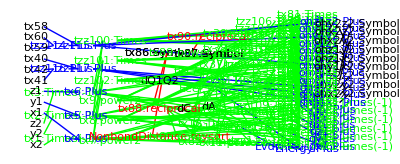

```mathematica
packGraph[nbPack]
```

## Dihedral angle

## Setup the torsion term

```mathematica
Clear[phi,CosNPhi,SinNPhi,Phi];
```

```mathematica
ri = { x1, y1, z1};
rj = { x2, y2, z2};
rk = { x3, y3, z3 };
rl = {x4, y4, z4};
r = Flatten[{ri,rj,rk,rl}];
```

```mathematica
vecLen[a_] := Sqrt[Dot[a,a]];
```

```mathematica
F = ri - rj;
G = rj - rk;
H = rl - rk;
```

```mathematica
A = Cross[F,G];
```

```mathematica
B = Cross[H,G];
```

```mathematica
lenA = vecLen[A];
lenB = vecLen[B];
```

```mathematica
reciprocalLenA = reciprocal[lenA];
reciprocalLenB = reciprocal[lenB];
```

```mathematica
dihedralVarNames = { 
{x1,x,I1,0,DPhiDri},
{y1,y,I1,1,DPhiDri},
{z1,z,I1,2,DPhiDri},
{x2,x,I2,0,DPhiDrj},
{y2,y,I2,1,DPhiDrj},
{z2,z,I2,2,DPhiDrj},
{x3,x,I3,0,DPhiDrk},
{y3,y,I3,1,DPhiDrk},
{z3,z,I3,2,DPhiDrk},
{x4,x,I4,0,DPhiDrl},
{y4,y,I4,1,DPhiDrl},
{z4,z,I4,2,DPhiDrl}
};
```

```mathematica
dihedralSetupRules = {};
AppendTo[dihedralSetupRules,CCode["DIHEDRAL_SET_PARAMETER(sinPhase);"]];
AppendTo[dihedralSetupRules,CCode["DIHEDRAL_SET_PARAMETER(cosPhase);"]];AppendTo[dihedralSetupRules,CCode["DIHEDRAL_SET_PARAMETER(V);"]];
AppendTo[dihedralSetupRules,CCode["DIHEDRAL_SET_PARAMETER(DN);"]];AppendTo[dihedralSetupRules,CCode["DIHEDRAL_SET_PARAMETER(IN);"]];AppendTo[dihedralSetupRules,CCode["DIHEDRAL_SET_PARAMETER(I1);"]];
AppendTo[dihedralSetupRules,CCode["DIHEDRAL_SET_PARAMETER(I2);"]];
AppendTo[dihedralSetupRules,CCode["DIHEDRAL_SET_PARAMETER(I3);"]];
AppendTo[dihedralSetupRules,CCode["DIHEDRAL_SET_PARAMETER(I4);"]];
```

```mathematica
For[i=1,i≤Length[dihedralVarNames],i++,
str = "DIHEDRAL_SET_POSITION("<>ToString[dihedralVarNames[[i]][[1]]]<>","<>ToString[dihedralVarNames[[i]][[3]]]<>","<>ToString[dihedralVarNames[[i]][[4]]]<>");";
Print[str];
AppendTo[dihedralSetupRules,CCode[str]];
];
```

DIHEDRAL_SET_POSITION(x1,I1,0);

DIHEDRAL_SET_POSITION(y1,I1,1);

DIHEDRAL_SET_POSITION(z1,I1,2);

DIHEDRAL_SET_POSITION(x2,I2,0);

DIHEDRAL_SET_POSITION(y2,I2,1);

DIHEDRAL_SET_POSITION(z2,I2,2);

DIHEDRAL_SET_POSITION(x3,I3,0);

DIHEDRAL_SET_POSITION(y3,I3,1);

DIHEDRAL_SET_POSITION(z3,I3,2);

DIHEDRAL_SET_POSITION(x4,I4,0);

DIHEDRAL_SET_POSITION(y4,I4,1);

DIHEDRAL_SET_POSITION(z4,I4,2);

```mathematica
dihedralSetupRules//MatrixForm
```

(CCode[DIHEDRAL_SET_PARAMETER(sinPhase);]
CCode[DIHEDRAL_SET_PARAMETER(cosPhase);]
CCode[DIHEDRAL_SET_PARAMETER(V);]
CCode[DIHEDRAL_SET_PARAMETER(DN);]
CCode[DIHEDRAL_SET_PARAMETER(IN);]
CCode[DIHEDRAL_SET_PARAMETER(I1);]
CCode[DIHEDRAL_SET_PARAMETER(I2);]
CCode[DIHEDRAL_SET_PARAMETER(I3);]
CCode[DIHEDRAL_SET_PARAMETER(I4);]
CCode[DIHEDRAL_SET_POSITION(x1,I1,0);]
CCode[DIHEDRAL_SET_POSITION(y1,I1,1);]
CCode[DIHEDRAL_SET_POSITION(z1,I1,2);]
CCode[DIHEDRAL_SET_POSITION(x2,I2,0);]
CCode[DIHEDRAL_SET_POSITION(y2,I2,1);]
CCode[DIHEDRAL_SET_POSITION(z2,I2,2);]
CCode[DIHEDRAL_SET_POSITION(x3,I3,0);]
CCode[DIHEDRAL_SET_POSITION(y3,I3,1);]
CCode[DIHEDRAL_SET_POSITION(z3,I3,2);]
CCode[DIHEDRAL_SET_POSITION(x4,I4,0);]
CCode[DIHEDRAL_SET_POSITION(y4,I4,1);]
CCode[DIHEDRAL_SET_POSITION(z4,I4,2);])

```mathematica
dihedralCosPhiRules = {};
```

```mathematica
AppendTo[dihedralCosPhiRules,lenA->LenA];
AppendTo[dihedralCosPhiRules,lenB->LenB];
AppendTo[dihedralCosPhiRules,reciprocalLenA->ReciprocalLenA];
AppendTo[dihedralCosPhiRules,reciprocalLenB->ReciprocalLenB];
```

```mathematica
AppendTo[dihedralCosPhiRules,CCode["if (fabs(LenA)<TENM3) ReciprocalLenA = 0.0;"]];
AppendTo[dihedralCosPhiRules,CCode["if (fabs(LenB)<TENM3) ReciprocalLenB = 0.0;"]];
```

```mathematica
recLenArecLenB = ReciprocalLenA*ReciprocalLenB;
```

```mathematica
AppendTo[dihedralCosPhiRules,recLenArecLenB->RecLenARecLenB];
```

```mathematica
AppendTo[dihedralCosPhiRules,CCode["EraseLinearDihedral = 1.0;"]];
AppendTo[dihedralCosPhiRules,CCode["if (RecLenARecLenB==0.0) EraseLinearDihedral = 0.0;"]];
```

```mathematica
cosPhi = A.B*(RecLenARecLenB);
sinPhi = vecLen[G]*RecLenARecLenB*Dot[A,H];
```

```mathematica
AppendTo[dihedralCosPhiRules,cosPhi->CosPhi];
AppendTo[dihedralCosPhiRules,sinPhi->SinPhi];
```

```mathematica
AppendTo[dihedralCosPhiRules,CCode["CosPhi=MAX(-1.0,MIN(1.0,CosPhi));"]];
```

phi = ArcCos[CosPhi];

AppendTo[dihedralEnergyRules, phi -> Phi]; (* I don't think I need to evaluate Phi *)

At this point we need to calculate SinNPhi and CosNPhi and we use the function calculateSinNPhiCosNPhi in both C and Mathematica.Insert function sinNPhiCosNPhi[N, &sinNPhi, &cosNPhi, sinPhi, cosPhi] into evaluation

```mathematica
dihedralEnergyRules = dihedralCosPhiRules;
```

```mathematica
AppendTo[dihedralEnergyRules,MathCode["CosNPhi = mathCosNPhi[IN,SinPhi,CosPhi];"]];
AppendTo[dihedralEnergyRules,MathCode["SinNPhi = mathSinNPhi[IN,SinPhi,CosPhi];"]];
```

```mathematica
If[DebugDihedral,
AppendTo[dihedralEnergyRules,MathCode["If[CosPhi>0.1,Phi=ArcSin[SinPhi],
					Phi=ArcCos[CosPhi]*Sign[SinPhi]];"]];
AppendTo[dihedralEnergyRules,CCode["if(CosPhi>0.1){Phi=asin(SinPhi);}else
					{Phi=acos(CosPhi)*SIGN(SinPhi);}"]];
];
```

```mathematica
AppendTo[dihedralEnergyRules,CCode["sinNPhiCosNPhi(IN, &SinNPhi, &CosNPhi, SinPhi, CosPhi);"]];
```

Sum and difference formulas
sin (A + B) = sin A cos B + cos A sin B
sin (A - B) = sin A cos B - cos A sin B
cos (A + B) = cos A cos B - sin A sin B
cos (A - B) = cos A cos B + sin A sin B

```mathematica
cosNPhiPhase =CosNPhi* cosPhase+SinNPhi*sinPhase;
sinNPhiPhase=SinNPhi*cosPhase-CosNPhi*sinPhase;
```

```mathematica
dihedralDeviation = 1.0+cosNPhiPhase; (*between 0.0 and 2.0*)
```

```mathematica
fnETorsion = EraseLinearDihedral * V (dihedralDeviation)
```

EraseLinearDihedral (1.+CosNPhi cosPhase+SinNPhi sinPhase) V

fnETorsion = EraseLinearDihedral * V (1.0 + Cos[DN Phi - phase]);

```mathematica
AppendTo[dihedralEnergyRules,Assign[DihedralDeviation,dihedralDeviation]];
AppendTo[dihedralEnergyRules,fnETorsion->Energy];
AppendTo[dihedralEnergyRules,EnergyAccumulate["DIHEDRAL",Energy]];
dihedralOutputs = {};
AppendTo[dihedralOutputs,Energy];
```

```mathematica
dihedralInputs = Flatten[{ri,rj,rk,rl,{V,DN,IN,cosPhase, sinPhase}}]
```

{x1,y1,z1,x2,y2,z2,x3,y3,z3,x4,y4,z4,V,DN,IN,cosPhase,sinPhase}

```mathematica
dihedralEnergyFn = fnETorsion/.{Phi->phi}
```

EraseLinearDihedral (1.+CosNPhi cosPhase+SinNPhi sinPhase) V

```mathematica
dETorsiondPhi = -EraseLinearDihedral*V*DN*sinNPhiPhase;
```

```mathematica
dihedralGradientRules = {}
```

{}

```mathematica
AppendTo[dihedralGradientRules, Assign[DeDPhi, dETorsiondPhi]];
```

```mathematica
DPhiDri = (-vecLen[G]/(A.A)A);
```

```mathematica
DPhiDrj = (vecLen[G]/(A.A)A+(F.G)/(A.A*vecLen[G])A-(H.G)/(B.B*vecLen[G])B);
```

```mathematica
DPhiDrk =((H.G)/(B.B*vecLen[G])B-(F.G)/(A.A*vecLen[G])A-vecLen[G]/(B.B)B);
```

```mathematica
DPhiDrl = (vecLen[G]/(B.B)B);
```

```mathematica
dPhidr = {};
```

```mathematica
AppendOneDihedralGradientForce[rawMacroPrefix_,be_,dPhidr_,outputs_,rawNameInfo_,rawdEdPhi_]:=Block[
	{fn,gradName,zforceName,nameRules,
	dEdPhi = Evaluate[rawdEdPhi],
	nameInfo=Evaluate[rawNameInfo],
	macroPrefix=Evaluate[rawMacroPrefix],var},
	nameRules = ExtractNames[nameInfo];
	var = Name/.nameRules;
	gradName = Symbol["g"<>ToString[var]];
	zforceName = Symbol["f"<>ToString[var]];
	fn = (Func/.nameRules)[[(Offset/.nameRules)+1]];
	AppendTo[dPhidr,fn];
	AppendTo[be,Assign[gradName,fn*dEdPhi]];
	AppendTo[be,Assign[zforceName,-gradName]];
	AppendTo[be,ForceAccumulate[macroPrefix,nameRules,zforceName]];
	AppendTo[outputs,zforceName];
];
SetAttributes[AppendOneDihedralGradientForce,HoldAll];
```

```mathematica
AppendDihedralGradientForce[rawMacroPrefix_,be_,dPhidr_,outputs_,rawNames_,rawdEdPhi_]:=Block[
	{macroPrefix=Evaluate[rawMacroPrefix],
	dEdPhi = Evaluate[rawdEdPhi],
	names = Evaluate[rawNames]},
	For[i=1,i≤Length[names],i++,
		Print["Appending gradient force for name: ", names[[i]][[1]]];
		AppendOneDihedralGradientForce[macroPrefix,be,dPhidr,outputs,names[[i]],dEdPhi];
	];
];
SetAttributes[AppendDihedralGradientForce,HoldAll];
```

```mathematica
AppendDihedralGradientForce["DIHEDRAL",dihedralGradientRules,dPhidr,dihedralOutputs,dihedralVarNames,DeDPhi];
```

Appending gradient force for name: x1

Appending gradient force for name: y1

Appending gradient force for name: z1

Appending gradient force for name: x2

Appending gradient force for name: y2

Appending gradient force for name: z2

Appending gradient force for name: x3

Appending gradient force for name: y3

Appending gradient force for name: z3

Appending gradient force for name: x4

Appending gradient force for name: y4

Appending gradient force for name: z4

#### Now dPhidr contains the vector derivative of Phi wrt every component in (r)

```mathematica
Length[dPhidr]
```

12

## Calculate the Second derivatives of d2Edr2

```mathematica
OuterVector[a_,b_] := Outer[Times,a,b];
```

```mathematica
OverlayMatrix[phiMatrix_,xo_,yo_,mat_]:=Block[{x,y,xa,ya},
	For[x=1,x≤3,x++,
		For[y=1,y≤3,y++,
			xa = (xo-1)*3+x;
			ya = (yo-1)*3+y;
			Print["Filling matrix[",xa,",",ya,"] := mat[",x,",",y,"];"];
			phiMatrix[[xa,ya]]= mat[[x]][[y]];
			If[xa≠ya,phiMatrix[[ya,xa]]= mat[[x]][[y]]];
		];
	];
];
SetAttributes[OverlayMatrix,HoldFirst];
```

```mathematica
OverlaySymmetricMatrix[phiMatrix_,xo_,yo_,mat_]:=Block[{},
	OverlayMatrix[phiMatrix,xo,yo,mat];
];
SetAttributes[OverlaySymmetricMatrix,HoldFirst];
```

```mathematica
(*According to the paper, this is what the Outer product of two matrices should be *)
MatrixOuter[a_,b_] := Block[{m},
m = Table[Table[0,{Length[a]}],{Length[b]}];
For[i=1,i≤Length[a],i++,
For[j=1,j≤Length[a],j++,
m[[i,j]]=a[[i]].b[[j]];
];
];
m
];
```

```mathematica
dPhi2dFGHdFGH = Table[Table[0,{9}],{9}];
```

```mathematica
dPhi2dFGHdFGH//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*Equation 32*)
dPhi2dFdF=vecLen[G]/((A.A)(A.A))(OuterVector[A,Cross[G,A]]+OuterVector[Cross[G,A],A]);
OverlaySymmetricMatrix[dPhi2dFGHdFGH,1,1,dPhi2dFdF];
```

Filling matrix[1,1] := mat[1,1];

Filling matrix[1,2] := mat[1,2];

Filling matrix[1,3] := mat[1,3];

Filling matrix[2,1] := mat[2,1];

Filling matrix[2,2] := mat[2,2];

Filling matrix[2,3] := mat[2,3];

Filling matrix[3,1] := mat[3,1];

Filling matrix[3,2] := mat[3,2];

Filling matrix[3,3] := mat[3,3];

```mathematica
If[DebugDihedral,1]
```

If[DebugDihedral,1]

```mathematica
(*Equation 33*)
dPhi2dHdH=(-vecLen[G])/((B.B)(B.B))(OuterVector[B,Cross[G,B]]+OuterVector[Cross[G,B],B]);
OverlaySymmetricMatrix[dPhi2dFGHdFGH,3,3,dPhi2dHdH];
```

Filling matrix[7,7] := mat[1,1];

Filling matrix[7,8] := mat[1,2];

Filling matrix[7,9] := mat[1,3];

Filling matrix[8,7] := mat[2,1];

Filling matrix[8,8] := mat[2,2];

Filling matrix[8,9] := mat[2,3];

Filling matrix[9,7] := mat[3,1];

Filling matrix[9,8] := mat[3,2];

Filling matrix[9,9] := mat[3,3];

```mathematica
(*Equation 38, this one has the weird subscripts but I'm just going to assume its simple*)
dPhi2dFdG = 1/(vecLen[G](A.A)(A.A))((G.G)OuterVector[Cross[A,F](*F*),A(*G*)]+(F.G)OuterVector[A(*F*),Cross[A,G](*G*)]);
OverlaySymmetricMatrix[dPhi2dFGHdFGH,1,2,dPhi2dFdG];
```

Filling matrix[1,4] := mat[1,1];

Filling matrix[1,5] := mat[1,2];

Filling matrix[1,6] := mat[1,3];

Filling matrix[2,4] := mat[2,1];

Filling matrix[2,5] := mat[2,2];

Filling matrix[2,6] := mat[2,3];

Filling matrix[3,4] := mat[3,1];

Filling matrix[3,5] := mat[3,2];

Filling matrix[3,6] := mat[3,3];

#### Equation (39), this one needs to be transposed wrt the equation described in the paper.

```mathematica
dPhi2dGdH =Transpose[-1/(vecLen[G](B.B)(B.B))((G.G)OuterVector[Cross[B,H](*H*),B(*G*)]+(H.G)OuterVector[B(*H*),Cross[B,G](*G*)])];OverlaySymmetricMatrix[dPhi2dFGHdFGH,2,3,dPhi2dGdH];
```

Filling matrix[4,7] := mat[1,1];

Filling matrix[4,8] := mat[1,2];

Filling matrix[4,9] := mat[1,3];

Filling matrix[5,7] := mat[2,1];

Filling matrix[5,8] := mat[2,2];

Filling matrix[5,9] := mat[2,3];

Filling matrix[6,7] := mat[3,1];

Filling matrix[6,8] := mat[3,2];

Filling matrix[6,9] := mat[3,3];

```mathematica
(*Equation 40*)
dPhi2dFdH = Table[Table[0,{3}],{3}];
```

```mathematica
OverlaySymmetricMatrix[dPhi2dFGHdFGH,1,3,dPhi2dFdH]
```

Filling matrix[1,7] := mat[1,1];

Filling matrix[1,8] := mat[1,2];

Filling matrix[1,9] := mat[1,3];

Filling matrix[2,7] := mat[2,1];

Filling matrix[2,8] := mat[2,2];

Filling matrix[2,9] := mat[2,3];

Filling matrix[3,7] := mat[3,1];

Filling matrix[3,8] := mat[3,2];

Filling matrix[3,9] := mat[3,3];

```mathematica
(*Equation 44*)
dPhi2dGdG=(1/(2(vecLen[G]^3)(A.A))(OuterVector[Cross[G,A],A]+OuterVector[A,Cross[G,A]]))+((F.G)/(vecLen[G](A.A)(A.A))(OuterVector[A,Cross[F,A]]+OuterVector[Cross[F,A],A]))+(-1/(2(vecLen[G]^3)(B.B))(OuterVector[Cross[G,B],B]+OuterVector[B,Cross[G,B]]))+((-(H.G))/(vecLen[G](B.B)(B.B))(OuterVector[B,Cross[H,B]]+OuterVector[Cross[H,B],B]));
```

```mathematica
OverlaySymmetricMatrix[dPhi2dFGHdFGH,2,2,dPhi2dGdG];
```

Filling matrix[4,4] := mat[1,1];

Filling matrix[4,5] := mat[1,2];

Filling matrix[4,6] := mat[1,3];

Filling matrix[5,4] := mat[2,1];

Filling matrix[5,5] := mat[2,2];

Filling matrix[5,6] := mat[2,3];

Filling matrix[6,4] := mat[3,1];

Filling matrix[6,5] := mat[3,2];

Filling matrix[6,6] := mat[3,3];

```mathematica
Dimensions[dPhi2dFGHdFGH]
```

{9,9}

#### At this point (dPhi2dFGHdFGH) should represent the first term in equation 29

```mathematica
(dFGHdr=D[Flatten[{F,G,H}],{Flatten[{ri,rj,rk,rl}]}])//MatrixForm
```

(1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1)

#### Let' s try a scalar product between dPhi2dFGHdFGH and dFGHdr

```mathematica
dihedralProd1 = dPhi2dFGHdFGH.dFGHdr;
```

```mathematica
Dimensions[dihedralProd1]
```

{9,12}

#### Now try a matrix outer product between (prod1) and dFGHdr.

```mathematica
d2Phidr2 = MatrixOuter[Transpose[dihedralProd1],Transpose[dFGHdr]];
```

```mathematica
Dimensions[d2Phidr2]
```

{12,12}

#### d2Phidr2 Should contain the product of equation 29

```mathematica
Transpose[dFGHdr]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
(*dETorsiondPhi = -EraseLinearDihedral*dihedralScale*V*DN*sinNPhiPhase;*)
```

## Assemble equation 28, the final equation for the second derivative, it should be a 12x12 matrix

```mathematica
d2EdPhi2 = -V*DN*DN*cosNPhiPhase;
```

```mathematica
d2Edr2 = OuterVector[(d2EdPhi2*dPhidr),dPhidr]+DeDPhi*d2Phidr2;
```

```mathematica
Dimensions[d2Edr2]
```

{12,12}

#### Assemble the names of the second derivatives

dihedralVarNames = { 
   {x1, x, I1, 0, DPhiDri},
   {y1, y, I1, 1, DPhiDri},
   {z1, z, I1, 2, DPhiDri},
   {x2, x, I2, 0, DPhiDrj},
   {y2, y, I2, 1, DPhiDrj},
   {z2, z, I2, 2, DPhiDrj},
   {x3, x, I3, 0, DPhiDrk},
   {y3, y, I3, 1, DPhiDrk},
   {z3, z, I3, 2, DPhiDrk},
   {x4, x, I4, 0, DPhiDrl},
   {y4, y, I4, 1, DPhiDrl},
   {z4, z, I4, 2, DPhiDrl}
   };

#### Setup the Diagonal Hessian rules

```mathematica
AppendDihedralOneHessianElement[macroPrefix_, be_, outputs_,hessianStructure_, rawHessianFn_, names_, i_, j_] := Module[
   	{name1Info, name2Info, var1Name, var2Name,hessianName,prefix, hess},
   	name1Info = ExtractNames[names[[i]]];
   	name2Info = ExtractNames[names[[j]]];
   	var1Name = Name /. name1Info;
   	var2Name = Name /. name2Info;
		If[i==j,prefix="d",prefix="o"];
   	hessianName = Symbol[prefix<>"h" <> ToString[var1Name] <> ToString[var2Name]];
   	hess = Evaluate[rawHessianFn][[i,j]];
   	AppendTo[be, Assign[hessianName, hess]];
   	AppendTo[outputs, hessianName];
   	AppendTo[be, HessianAccumulate[macroPrefix, name1Info, name2Info, hessianName]];
   	Print["Appended hessian element (", j, ",", i, ") for variable: ", ToString[hessianName]];
		hessianStructure[[i,j]]=Length[outputs];
		If [i≠j,hessianStructure[[j,i]]=Length[outputs]];
   ];
SetAttributes[AppendDihedralOneHessianElement, HoldAll];
```

```mathematica
AppendDihedralDiagonalHessian[macroPrefix_,be_,outputs_,hessianStructure_,rawHessianFn_,names_]:= Module[ {i},
	For[i=1,i≤Length[d2Edr2],i++,
		AppendDihedralOneHessianElement[macroPrefix<>"_DIAGONAL",be,outputs,hessianStructure,rawHessianFn,names,i,i];
	];
];
SetAttributes[AppendDihedralDiagonalHessian, HoldAll];
```

```mathematica
Length[d2Edr2]
```

12

For[i = 1, i <= Length[d2Edr2], i++,
  AppendDihedralOneHessianElement["DIHEDRAL", dihedralDiagonalHessianRules, dihedralOutputs, d2Edr2, dihedralVarNames, i, i];
  ];

```mathematica
dihedralHessian = Table[Table[0,{12}],{12}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
dihedralDiagonalHessianRules = {};AppendDihedralDiagonalHessian["DIHEDRAL",dihedralDiagonalHessianRules,dihedralOutputs,dihedralHessian,d2Edr2,dihedralVarNames];
```

Appended hessian element (1,1) for variable: dhx1x1

Appended hessian element (2,2) for variable: dhy1y1

Appended hessian element (3,3) for variable: dhz1z1

Appended hessian element (4,4) for variable: dhx2x2

Appended hessian element (5,5) for variable: dhy2y2

Appended hessian element (6,6) for variable: dhz2z2

Appended hessian element (7,7) for variable: dhx3x3

Appended hessian element (8,8) for variable: dhy3y3

Appended hessian element (9,9) for variable: dhz3z3

Appended hessian element (10,10) for variable: dhx4x4

Appended hessian element (11,11) for variable: dhy4y4

Appended hessian element (12,12) for variable: dhz4z4

#### Setup the Off Diagonal Hessian rules

```mathematica
AppendDihedralOffDiagonalHessian[macroPrefix_,be_,outputs_,hessianStructure_,rawHessianFn_,names_]:= Module[ {i,j},
	For[i=1,i≤Length[d2Edr2]-1,i++,
		For[j=i+1,j≤Length[d2Edr2],j++,
			AppendDihedralOneHessianElement[macroPrefix<>"_OFF_DIAGONAL",be,outputs,hessianStructure,rawHessianFn,names,i,j];
		];
	];
];
SetAttributes[AppendDihedralOffDiagonalHessian, HoldAll];
```

```mathematica
dihedralOffDiagonalHessianRules = {};AppendDihedralOffDiagonalHessian["DIHEDRAL",dihedralOffDiagonalHessianRules,dihedralOutputs,dihedralHessian,d2Edr2,dihedralVarNames];
```

Appended hessian element (2,1) for variable: ohx1y1

Appended hessian element (3,1) for variable: ohx1z1

Appended hessian element (4,1) for variable: ohx1x2

Appended hessian element (5,1) for variable: ohx1y2

Appended hessian element (6,1) for variable: ohx1z2

Appended hessian element (7,1) for variable: ohx1x3

Appended hessian element (8,1) for variable: ohx1y3

Appended hessian element (9,1) for variable: ohx1z3

Appended hessian element (10,1) for variable: ohx1x4

Appended hessian element (11,1) for variable: ohx1y4

Appended hessian element (12,1) for variable: ohx1z4

Appended hessian element (3,2) for variable: ohy1z1

Appended hessian element (4,2) for variable: ohy1x2

Appended hessian element (5,2) for variable: ohy1y2

Appended hessian element (6,2) for variable: ohy1z2

Appended hessian element (7,2) for variable: ohy1x3

Appended hessian element (8,2) for variable: ohy1y3

Appended hessian element (9,2) for variable: ohy1z3

Appended hessian element (10,2) for variable: ohy1x4

Appended hessian element (11,2) for variable: ohy1y4

Appended hessian element (12,2) for variable: ohy1z4

Appended hessian element (4,3) for variable: ohz1x2

Appended hessian element (5,3) for variable: ohz1y2

Appended hessian element (6,3) for variable: ohz1z2

Appended hessian element (7,3) for variable: ohz1x3

Appended hessian element (8,3) for variable: ohz1y3

Appended hessian element (9,3) for variable: ohz1z3

Appended hessian element (10,3) for variable: ohz1x4

Appended hessian element (11,3) for variable: ohz1y4

Appended hessian element (12,3) for variable: ohz1z4

Appended hessian element (5,4) for variable: ohx2y2

Appended hessian element (6,4) for variable: ohx2z2

Appended hessian element (7,4) for variable: ohx2x3

Appended hessian element (8,4) for variable: ohx2y3

Appended hessian element (9,4) for variable: ohx2z3

Appended hessian element (10,4) for variable: ohx2x4

Appended hessian element (11,4) for variable: ohx2y4

Appended hessian element (12,4) for variable: ohx2z4

Appended hessian element (6,5) for variable: ohy2z2

Appended hessian element (7,5) for variable: ohy2x3

Appended hessian element (8,5) for variable: ohy2y3

Appended hessian element (9,5) for variable: ohy2z3

Appended hessian element (10,5) for variable: ohy2x4

Appended hessian element (11,5) for variable: ohy2y4

Appended hessian element (12,5) for variable: ohy2z4

Appended hessian element (7,6) for variable: ohz2x3

Appended hessian element (8,6) for variable: ohz2y3

Appended hessian element (9,6) for variable: ohz2z3

Appended hessian element (10,6) for variable: ohz2x4

Appended hessian element (11,6) for variable: ohz2y4

Appended hessian element (12,6) for variable: ohz2z4

Appended hessian element (8,7) for variable: ohx3y3

Appended hessian element (9,7) for variable: ohx3z3

Appended hessian element (10,7) for variable: ohx3x4

Appended hessian element (11,7) for variable: ohx3y4

Appended hessian element (12,7) for variable: ohx3z4

Appended hessian element (9,8) for variable: ohy3z3

Appended hessian element (10,8) for variable: ohy3x4

Appended hessian element (11,8) for variable: ohy3y4

Appended hessian element (12,8) for variable: ohy3z4

Appended hessian element (10,9) for variable: ohz3x4

Appended hessian element (11,9) for variable: ohz3y4

Appended hessian element (12,9) for variable: ohz3z4

Appended hessian element (11,10) for variable: ohx4y4

Appended hessian element (12,10) for variable: ohx4z4

Appended hessian element (12,11) for variable: ohy4z4

For[i = 1, i <= Length[d2Edr2] - 1, i++,
  For[j = i + 1, j <= Length[d2Edr2], j++,
    AppendDihedralOneHessianElement["DIHEDRAL", dihedralOffDiagonalHessianRules, dihedralOutputs, d2Edr2, dihedralVarNames, i, j];
    ];
  ];

```mathematica
dihedralAllRules = {};
AppendTo[dihedralAllRules,dihedralSetupRules];
AppendTo[dihedralAllRules,dihedralEnergyRules];
AppendTo[dihedralAllRules,CCode["#ifdef DIHEDRAL_CALC_FORCE //["]];
AppendTo[dihedralAllRules,CCode["if (calcForce ) {" ]];
AppendTo[dihedralAllRules,dihedralGradientRules];
AppendTo[dihedralAllRules,CCode["#ifdef DIHEDRAL_CALC_DIAGONAL_HESSIAN //["]];
AppendTo[dihedralAllRules,CCode["if (calcDiagonalHessian) {" ]];
AppendTo[dihedralAllRules,dihedralDiagonalHessianRules];
AppendTo[dihedralAllRules,CCode["#ifdef DIHEDRAL_CALC_OFF_DIAGONAL_HESSIAN //["]];
AppendTo[dihedralAllRules,CCode["if (calcOffDiagonalHessian) { "]];
AppendTo[dihedralAllRules,dihedralOffDiagonalHessianRules];
AppendTo[dihedralAllRules,CCode["} /*calcOffDiagonalHessian*/"]];
AppendTo[dihedralAllRules,CCode["#endif // DIHEDRAL_CALC_OFF_DIAGONAL_HESSIAN ]"]];
AppendTo[dihedralAllRules,CCode["} /*calcDiagonalHessian*/"]];
AppendTo[dihedralAllRules,CCode["#endif // DIHEDRAL_CALC_DIAGONAL_HESSIAN ]"]];
AppendTo[dihedralAllRules,CCode["} /*calcForce*/"]];
AppendTo[dihedralAllRules,CCode["#endif // DIHEDRAL_CALC_FORCE ]"]];
```

```mathematica
AppendTo[dihedralOutputs,DihedralDeviation];
```

```mathematica
dihedralFlattenedRules = Flatten[dihedralAllRules];
```

```mathematica
If[DebugDihedral,
AppendTo[dihedralOutputs,Phi];
];
```

```mathematica
dihedralPack0 = {
Name->"Dihedral",
AdditionalCDeclares->"",
EnergyFunction->"NotUsed",
DerivativeVariables->{x1,y1,z1,x2,y2,z2,x3,y3,z3,x4,y4,z4},
HessianStructure->dihedralHessian,
Rules->dihedralFlattenedRules,
Input->dihedralInputs,
Output->dihedralOutputs
};
```

```mathematica
PlusOptimize = False;
TimesOptimize = False;
```

```mathematica
writeOutputVariablesForDebugging[dihedralPack0];
```

Writing finite difference debug code to: _Dihedral_debugFiniteDifference.cc

Writing debug variable declares to: _Dihedral_debugEvalDeclares.cc

Writing xml output debug code to: _Dihedral_debugEvalSerialize.cc

Writing set variables debug code to: _Dihedral_debugEvalSet.cc

```mathematica
dihedralPack=packOptimize[dihedralPack0];
```

Set TimesSimplify and PlusSimplify to turn these simplifications off and on

PlusOptimize = False

TimesOptimize = False

Writing declares to file: _Dihedral_termDeclares.cc

Writing code to file: _Dihedral_termCode.cc

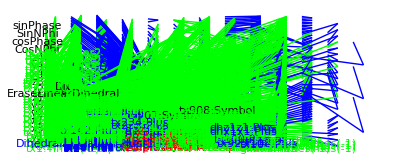

```mathematica
packGraph[dihedralPack]
```

## An improved improper restraint with no discontinuities

```mathematica
improperRestraintSetupRules = {};
AppendTo[improperRestraintSetupRules,CCode["IMPROPER_RESTRAINT_SET_PARAMETER(K);"]];
AppendTo[improperRestraintSetupRules,CCode["IMPROPER_RESTRAINT_SET_PARAMETER(U);"]];AppendTo[improperRestraintSetupRules,CCode["IMPROPER_RESTRAINT_SET_PARAMETER(L);"]];
AppendTo[improperRestraintSetupRules,CCode["IMPROPER_RESTRAINT_SET_PARAMETER(I1);"]];
AppendTo[improperRestraintSetupRules,CCode["IMPROPER_RESTRAINT_SET_PARAMETER(I2);"]];
AppendTo[improperRestraintSetupRules,CCode["IMPROPER_RESTRAINT_SET_PARAMETER(I3);"]];
AppendTo[improperRestraintSetupRules,CCode["IMPROPER_RESTRAINT_SET_PARAMETER(I4);"]];
```

```mathematica
For[i=1,i≤Length[dihedralVarNames],i++,
str = "IMPROPER_RESTRAINT_SET_POSITION("<>ToString[dihedralVarNames[[i]][[1]]]<>","<>ToString[dihedralVarNames[[i]][[3]]]<>","<>ToString[dihedralVarNames[[i]][[4]]]<>");";
Print[str];
AppendTo[improperRestraintSetupRules,CCode[str]];
];
```

IMPROPER_RESTRAINT_SET_POSITION(x1,I1,0);

IMPROPER_RESTRAINT_SET_POSITION(y1,I1,1);

IMPROPER_RESTRAINT_SET_POSITION(z1,I1,2);

IMPROPER_RESTRAINT_SET_POSITION(x2,I2,0);

IMPROPER_RESTRAINT_SET_POSITION(y2,I2,1);

IMPROPER_RESTRAINT_SET_POSITION(z2,I2,2);

IMPROPER_RESTRAINT_SET_POSITION(x3,I3,0);

IMPROPER_RESTRAINT_SET_POSITION(y3,I3,1);

IMPROPER_RESTRAINT_SET_POSITION(z3,I3,2);

IMPROPER_RESTRAINT_SET_POSITION(x4,I4,0);

IMPROPER_RESTRAINT_SET_POSITION(y4,I4,1);

IMPROPER_RESTRAINT_SET_POSITION(z4,I4,2);

```mathematica
improperRestraintSetupRules//MatrixForm
```

(CCode[IMPROPER_RESTRAINT_SET_PARAMETER(K);]
CCode[IMPROPER_RESTRAINT_SET_PARAMETER(U);]
CCode[IMPROPER_RESTRAINT_SET_PARAMETER(L);]
CCode[IMPROPER_RESTRAINT_SET_PARAMETER(I1);]
CCode[IMPROPER_RESTRAINT_SET_PARAMETER(I2);]
CCode[IMPROPER_RESTRAINT_SET_PARAMETER(I3);]
CCode[IMPROPER_RESTRAINT_SET_PARAMETER(I4);]
CCode[IMPROPER_RESTRAINT_SET_POSITION(x1,I1,0);]
CCode[IMPROPER_RESTRAINT_SET_POSITION(y1,I1,1);]
CCode[IMPROPER_RESTRAINT_SET_POSITION(z1,I1,2);]
CCode[IMPROPER_RESTRAINT_SET_POSITION(x2,I2,0);]
CCode[IMPROPER_RESTRAINT_SET_POSITION(y2,I2,1);]
CCode[IMPROPER_RESTRAINT_SET_POSITION(z2,I2,2);]
CCode[IMPROPER_RESTRAINT_SET_POSITION(x3,I3,0);]
CCode[IMPROPER_RESTRAINT_SET_POSITION(y3,I3,1);]
CCode[IMPROPER_RESTRAINT_SET_POSITION(z3,I3,2);]
CCode[IMPROPER_RESTRAINT_SET_POSITION(x4,I4,0);]
CCode[IMPROPER_RESTRAINT_SET_POSITION(y4,I4,1);]
CCode[IMPROPER_RESTRAINT_SET_POSITION(z4,I4,2);])

```mathematica
Clear[Phi,CosNPhi,SinNPhi];
```

### Here is what it looks like

```mathematica
rad[h_] := h*0.0174533
```

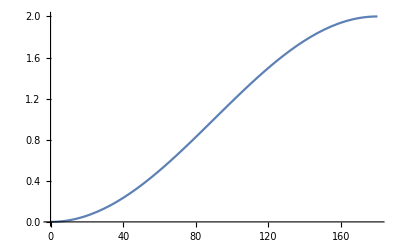

```mathematica
Plot[1-Cos[phi//rad],{phi,0,180}]
```

```mathematica
rawRestraintFn[phi_,L_,U_] := (1-Cos[((phi-L)/(U-L)360)//rad])^3
```

```mathematica
otherRestraintFn[phi_,L_,U_] := (1-Cos[((If[phi>=L,phi,phi+360]-L)/(U+360-L)360)//rad])^3
```

```mathematica
LGreaterThanU[phi_,L_,U_] :=Block[{},
If[(phi<L)&&(phi>U),
0.0,
otherRestraintFn[phi,L,U]
]
]
```

```mathematica
LLessThanU[phi_,L_,U_]:=If[(phi<L)||(phi>U),0.0,rawRestraintFn[phi,L,U]]
```

```mathematica
restraint[phi_,L_,U_]:=If[L<U,LLessThanU[phi,L,U],LGreaterThanU[phi,L,U]]
```

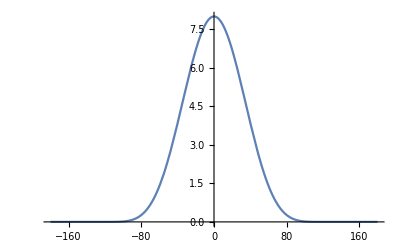

```mathematica
Plot[restraint[phi,-130,130],{phi,-180,180}]
```

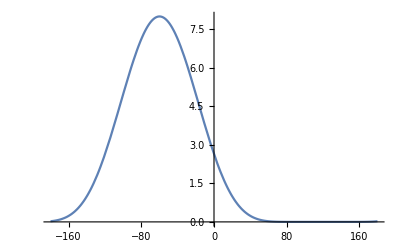

```mathematica
Plot[restraint[phi,140,100],{phi,-180,180},PlotRange->All]
```

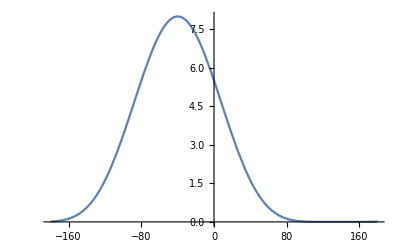

```mathematica
Plot[restraint[phi,140,140],{phi,-180,180},PlotRange->All]
```

Setup the improper torsion term
We reuse the code for the dihedral term,
specifically we start with:   dihedralCosPhiRules

```mathematica
Clear[Phi]
```

Sum and difference formulas
sin (A + B) = sin A cos B + cos A sin B
sin (A - B) = sin A cos B - cos A sin B
cos (A + B) = cos A cos B - sin A sin B
cos (A - B) = cos A cos B + sin A sin B

```mathematica
improperRestraintOutputs = {};
```

```mathematica
improperRestraintTestRules = dihedralCosPhiRules;
```

```mathematica
AppendTo[improperRestraintTestRules,MathCode["If[CosPhi>0.1,Phi=ArcSin[SinPhi],
					Phi=ArcCos[CosPhi]*Sign[SinPhi]];"]];
AppendTo[improperRestraintTestRules,CCode["if(CosPhi>0.1){Phi=asin(SinPhi);}else
					{Phi=acos(CosPhi)*SIGN(SinPhi);}"]];
```

#### At this point we have calculated Phi

```mathematica
AppendTo[improperRestraintTestRules,MathCode["RestraintActive = False;"]];
AppendTo[improperRestraintTestRules,CCode["RestraintActive=false;"]];
```

```mathematica
AppendTo[improperRestraintTestRules,MathCode["UShift = 0.0; PhiShift=0.0;"]];
AppendTo[improperRestraintTestRules,CCode["UShift = 0.0; PhiShift = 0.0;"]];
```

```mathematica
AppendTo[improperRestraintTestRules,MathCode["
If[ L<U && ((L<=Phi)&&(Phi<=U)), 
	RestraintActive = True;
	UShift = 0.0;
	PhiShift = 0.0;
];
"]];
AppendTo[improperRestraintTestRules,CCode[       "
if( L<U && (L<Phi)&&(Phi<U) ) {
	RestraintActive = true;
	UShift = 0.0;
	PhiShift = 0.0;
}"]];
```

```mathematica
AppendTo[improperRestraintTestRules,MathCode["
If[ U<=L && ((Phi<=U)||(Phi>=L)),
	RestraintActive = True;
	UShift = TWOPI;
	If[Phi>=L,
		PhiShift = 0.0;
	,
		PhiShift = TWOPI;
	];
];"]];
AppendTo[improperRestraintTestRules,CCode["
if ( U<=L && ((Phi<=U)||(Phi>=L))) {
	RestraintActive = true;
	UShift = TWOPI;
	if ( Phi>=L ) {
		PhiShift = 0.0;
	} else {
		PhiShift = TWOPI;
	}
}"]];
```

```mathematica
MacroCall[name_,value_] := CCode[name<>"("<>ToString[value]<>");"];
```

### At this point we have the improperRestraintTestRules defined

AppendTo[improperRestraintEnergyRules, MathCode["If[RestraintActive,"]];
AppendTo[improperRestraintEnergyRules, CCode["if(RestraintActive){"]];

```mathematica
improperRestraintEnergyRules = {};
```

```mathematica
psi = (Phi+PhiShift-L)/(U+UShift-L)TWOPI
```

((-L+Phi+PhiShift) TWOPI)/(-L+U+UShift)

```mathematica
AppendTo[improperRestraintEnergyRules,Assign[Psi,psi]];
```

```mathematica
fnEImproperRestraint = EraseLinearDihedral*K (1-Cos[Psi])^3
```

EraseLinearDihedral K (1-Cos[Psi])^3

```mathematica
AppendTo[improperRestraintEnergyRules,Assign[Energy,fnEImproperRestraint]];
```

```mathematica
AppendTo[improperRestraintOutputs,Energy];
AppendTo[improperRestraintEnergyRules,EnergyAccumulate["IMPROPER_RESTRAINT",Energy]];
```

#### Here we have the improperRestraintEnergyRules defined

```mathematica
improperRestraintInputs = Flatten[{ri,rj,rk,rl,{K,L,U}}]
```

{x1,y1,z1,x2,y2,z2,x3,y3,z3,x4,y4,z4,K,L,U}

```mathematica
fnEImproperRestraintWrtPhi = fnEImproperRestraint/.{Psi->psi}
```

EraseLinearDihedral K (1-Cos[((-L+Phi+PhiShift) TWOPI)/(-L+U+UShift)])^3

```mathematica
dEImproperRestraintDPhi= D[fnEImproperRestraintWrtPhi,Phi]
```

(3 EraseLinearDihedral K TWOPI (1-Cos[((-L+Phi+PhiShift) TWOPI)/(-L+U+UShift)])^2 Sin[((-L+Phi+PhiShift) TWOPI)/(-L+U+UShift)])/(-L+U+UShift)

```mathematica
d2EImproperRestraintDPhi2 = D[dEImproperRestraintDPhi,Phi]
```

(3 EraseLinearDihedral K TWOPI^2 (1-Cos[((-L+Phi+PhiShift) TWOPI)/(-L+U+UShift)])^2 Cos[((-L+Phi+PhiShift) TWOPI)/(-L+U+UShift)])/(-L+U+UShift)^2+(6 EraseLinearDihedral K TWOPI^2 (1-Cos[((-L+Phi+PhiShift) TWOPI)/(-L+U+UShift)]) Sin[((-L+Phi+PhiShift) TWOPI)/(-L+U+UShift)]^2)/(-L+U+UShift)^2

```mathematica
improperRestraintVarNames= dihedralVarNames;
```

```mathematica
improperRestraintGradientRules = {};
AppendTo[improperRestraintGradientRules,Assign[DEImproperRestraintDPhi,dEImproperRestraintDPhi]];
improperDPhiDr = {};
AppendDihedralGradientForce["IMPROPER_RESTRAINT",improperRestraintGradientRules,improperDPhiDr, improperRestraintOutputs, improperRestraintVarNames, DEImproperRestraintDPhi ];
```

Appending gradient force for name: x1

Appending gradient force for name: y1

Appending gradient force for name: z1

Appending gradient force for name: x2

Appending gradient force for name: y2

Appending gradient force for name: z2

Appending gradient force for name: x3

Appending gradient force for name: y3

Appending gradient force for name: z3

Appending gradient force for name: x4

Appending gradient force for name: y4

Appending gradient force for name: z4

```mathematica
improperRestraintD2Edr2 = OuterVector[(d2EImproperRestraintDPhi2*dPhidr),dPhidr]+dEImproperRestraintDPhi*d2Phidr2;
```

```mathematica
Dimensions[improperRestraintD2Edr2]
```

{12,12}

```mathematica
improperRestraintHessian = Table[Table[0,{12}],{12}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
improperRestraintDiagonalHessianRules = {};AppendDihedralDiagonalHessian["IMPROPER_RESTRAINT",improperRestraintDiagonalHessianRules,improperRestraintOutputs,improperRestraintHessian, improperRestraintD2Edr2,improperRestraintVarNames];
```

Appended hessian element (1,1) for variable: dhx1x1

Appended hessian element (2,2) for variable: dhy1y1

Appended hessian element (3,3) for variable: dhz1z1

Appended hessian element (4,4) for variable: dhx2x2

Appended hessian element (5,5) for variable: dhy2y2

Appended hessian element (6,6) for variable: dhz2z2

Appended hessian element (7,7) for variable: dhx3x3

Appended hessian element (8,8) for variable: dhy3y3

Appended hessian element (9,9) for variable: dhz3z3

Appended hessian element (10,10) for variable: dhx4x4

Appended hessian element (11,11) for variable: dhy4y4

Appended hessian element (12,12) for variable: dhz4z4

```mathematica
improperRestraintOffDiagonalHessianRules = {};AppendDihedralOffDiagonalHessian["IMPROPER_RESTRAINT",improperRestraintOffDiagonalHessianRules,improperRestraintOutputs,improperRestraintHessian,improperRestraintD2Edr2,improperRestraintVarNames];
```

Appended hessian element (2,1) for variable: ohx1y1

Appended hessian element (3,1) for variable: ohx1z1

Appended hessian element (4,1) for variable: ohx1x2

Appended hessian element (5,1) for variable: ohx1y2

Appended hessian element (6,1) for variable: ohx1z2

Appended hessian element (7,1) for variable: ohx1x3

Appended hessian element (8,1) for variable: ohx1y3

Appended hessian element (9,1) for variable: ohx1z3

Appended hessian element (10,1) for variable: ohx1x4

Appended hessian element (11,1) for variable: ohx1y4

Appended hessian element (12,1) for variable: ohx1z4

Appended hessian element (3,2) for variable: ohy1z1

Appended hessian element (4,2) for variable: ohy1x2

Appended hessian element (5,2) for variable: ohy1y2

Appended hessian element (6,2) for variable: ohy1z2

Appended hessian element (7,2) for variable: ohy1x3

Appended hessian element (8,2) for variable: ohy1y3

Appended hessian element (9,2) for variable: ohy1z3

Appended hessian element (10,2) for variable: ohy1x4

Appended hessian element (11,2) for variable: ohy1y4

Appended hessian element (12,2) for variable: ohy1z4

Appended hessian element (4,3) for variable: ohz1x2

Appended hessian element (5,3) for variable: ohz1y2

Appended hessian element (6,3) for variable: ohz1z2

Appended hessian element (7,3) for variable: ohz1x3

Appended hessian element (8,3) for variable: ohz1y3

Appended hessian element (9,3) for variable: ohz1z3

Appended hessian element (10,3) for variable: ohz1x4

Appended hessian element (11,3) for variable: ohz1y4

Appended hessian element (12,3) for variable: ohz1z4

Appended hessian element (5,4) for variable: ohx2y2

Appended hessian element (6,4) for variable: ohx2z2

Appended hessian element (7,4) for variable: ohx2x3

Appended hessian element (8,4) for variable: ohx2y3

Appended hessian element (9,4) for variable: ohx2z3

Appended hessian element (10,4) for variable: ohx2x4

Appended hessian element (11,4) for variable: ohx2y4

Appended hessian element (12,4) for variable: ohx2z4

Appended hessian element (6,5) for variable: ohy2z2

Appended hessian element (7,5) for variable: ohy2x3

Appended hessian element (8,5) for variable: ohy2y3

Appended hessian element (9,5) for variable: ohy2z3

Appended hessian element (10,5) for variable: ohy2x4

Appended hessian element (11,5) for variable: ohy2y4

Appended hessian element (12,5) for variable: ohy2z4

Appended hessian element (7,6) for variable: ohz2x3

Appended hessian element (8,6) for variable: ohz2y3

Appended hessian element (9,6) for variable: ohz2z3

Appended hessian element (10,6) for variable: ohz2x4

Appended hessian element (11,6) for variable: ohz2y4

Appended hessian element (12,6) for variable: ohz2z4

Appended hessian element (8,7) for variable: ohx3y3

Appended hessian element (9,7) for variable: ohx3z3

Appended hessian element (10,7) for variable: ohx3x4

Appended hessian element (11,7) for variable: ohx3y4

Appended hessian element (12,7) for variable: ohx3z4

Appended hessian element (9,8) for variable: ohy3z3

Appended hessian element (10,8) for variable: ohy3x4

Appended hessian element (11,8) for variable: ohy3y4

Appended hessian element (12,8) for variable: ohy3z4

Appended hessian element (10,9) for variable: ohz3x4

Appended hessian element (11,9) for variable: ohz3y4

Appended hessian element (12,9) for variable: ohz3z4

Appended hessian element (11,10) for variable: ohx4y4

Appended hessian element (12,10) for variable: ohx4z4

Appended hessian element (12,11) for variable: ohy4z4

```mathematica
InitializeOutputs[outputs_] := Block[{zeroOutputs},
	zeroOutputs = Map[ToString[#]<>"= 0.0;\n"&,outputs];
	Return[StringJoin[zeroOutputs]];
];
```

```mathematica
improperRestraintAllRules = {};
AppendTo[improperRestraintAllRules,improperRestraintSetupRules];
(* take out setting variables to zero *)
(* AppendTo[improperRestraintAllRules,CCode[InitializeOutputs[improperRestraintOutputs]]]; *)
AppendTo[improperRestraintAllRules,MathCode[InitializeOutputs[improperRestraintOutputs]]];
AppendTo[improperRestraintAllRules,improperRestraintTestRules];
AppendTo[improperRestraintAllRules,MathCode["If[RestraintActive," ]];
AppendTo[improperRestraintAllRules,CCode["if (RestraintActive ) {" ]];AppendTo[improperRestraintAllRules,improperRestraintEnergyRules];
AppendTo[improperRestraintAllRules,CCode["#ifdef IMPROPER_RESTRAINT_CALC_FORCE //["]];
AppendTo[improperRestraintAllRules,CCode["if (calcForce ) {" ]];
AppendTo[improperRestraintAllRules,improperRestraintGradientRules];
AppendTo[improperRestraintAllRules,CCode["#ifdef IMPROPER_RESTRAINT_CALC_DIAGONAL_HESSIAN //["]];
AppendTo[improperRestraintAllRules,CCode["if (calcDiagonalHessian) {" ]];
AppendTo[improperRestraintAllRules,improperRestraintDiagonalHessianRules];
AppendTo[improperRestraintAllRules,CCode["#ifdef IMPROPER_RESTRAINT_CALC_OFF_DIAGONAL_HESSIAN //["]];
AppendTo[improperRestraintAllRules,CCode["if (calcOffDiagonalHessian) { "]];
AppendTo[improperRestraintAllRules,improperRestraintOffDiagonalHessianRules];
AppendTo[improperRestraintAllRules,CCode["} /*calcOffDiagonalHessian*/"]];
AppendTo[improperRestraintAllRules,CCode["#endif //IMPROPER_RESTRAINT_CALC_OFF_DIAGONAL_HESSIAN ]"]];
AppendTo[improperRestraintAllRules,CCode["} /*calcDiagonalHessian*/"]];
AppendTo[improperRestraintAllRules,CCode["#endif //IMPROPER_RESTRAINT_CALC_DIAGONAL_HESSIAN ]"]];
AppendTo[improperRestraintAllRules,CCode["} /*calcForce*/"]];
AppendTo[improperRestraintAllRules,CCode["#endif //IMPROPER_RESTRAINT_CALC_FORCE ]"]];
AppendTo[improperRestraintAllRules,CCode["} /*RestraintActive*/"]];
AppendTo[improperRestraintAllRules,MacroCall["IMPROPER_RESTRAINT_PHI_SET",Phi]];
AppendTo[improperRestraintOutputs,Phi];
AppendTo[improperRestraintAllRules, MathCode["]; (*RestraintActive*)"]];
```

```mathematica
improperRestraintFlattenedRules = Flatten[improperRestraintAllRules];
```

```mathematica
improperRestraintOutputs
```

{Energy,fx1,fy1,fz1,fx2,fy2,fz2,fx3,fy3,fz3,fx4,fy4,fz4,dhx1x1,dhy1y1,dhz1z1,dhx2x2,dhy2y2,dhz2z2,dhx3x3,dhy3y3,dhz3z3,dhx4x4,dhy4y4,dhz4z4,ohx1y1,ohx1z1,ohx1x2,ohx1y2,ohx1z2,ohx1x3,ohx1y3,ohx1z3,ohx1x4,ohx1y4,ohx1z4,ohy1z1,ohy1x2,ohy1y2,ohy1z2,ohy1x3,ohy1y3,ohy1z3,ohy1x4,ohy1y4,ohy1z4,ohz1x2,ohz1y2,ohz1z2,ohz1x3,ohz1y3,ohz1z3,ohz1x4,ohz1y4,ohz1z4,ohx2y2,ohx2z2,ohx2x3,ohx2y3,ohx2z3,ohx2x4,ohx2y4,ohx2z4,ohy2z2,ohy2x3,ohy2y3,ohy2z3,ohy2x4,ohy2y4,ohy2z4,ohz2x3,ohz2y3,ohz2z3,ohz2x4,ohz2y4,ohz2z4,ohx3y3,ohx3z3,ohx3x4,ohx3y4,ohx3z4,ohy3z3,ohy3x4,ohy3y4,ohy3z4,ohz3x4,ohz3y4,ohz3z4,ohx4y4,ohx4z4,ohy4z4,Phi}

```mathematica
improperRestraintPack0 = {
Name->"ImproperRestraint",
AdditionalCDeclares->"",
DerivativeVariables->{x1,y1,z1,x2,y2,z2,x3,y3,z3,x4,y4,z4},
HessianStructure->improperRestraintHessian,
Rules->improperRestraintFlattenedRules,
Input->improperRestraintInputs,
Output->improperRestraintOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[improperRestraintPack0];
```

Writing finite difference debug code to: _ImproperRestraint_debugFiniteDifference.cc

Writing debug variable declares to: _ImproperRestraint_debugEvalDeclares.cc

Writing xml output debug code to: _ImproperRestraint_debugEvalSerialize.cc

Writing set variables debug code to: _ImproperRestraint_debugEvalSet.cc

```mathematica
improperRestraintPack=packOptimize[improperRestraintPack0];
```

Set TimesSimplify and PlusSimplify to turn these simplifications off and on

PlusOptimize = False

TimesOptimize = False

Writing declares to file: _ImproperRestraint_termDeclares.cc

Writing code to file: _ImproperRestraint_termCode.cc

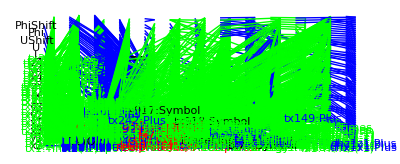

```mathematica
packGraph[improperRestraintPack]
```

## Chiral Restraint - Expand the gradient and Hessian.

```mathematica
Clear[x1,y1,z1,x2,y2,z2];
```

```mathematica
va = { x1, y1, z1};
vb = { x2, y2, z2 };
vc = { x3, y3, z3 };
vd = { x4, y4, z4 };
```

```mathematica
Clear[ac,bc,dc];
ac = va-vc;
bc = vb - vc;
dc = vd - vc;
```

```mathematica
Clear[K];
```

```mathematica
chiralRestraintTestFn =  K ((Cross[ac,bc].dc)/(vecLen[ac]vecLen[bc]vecLen[dc])+CO)^3
```

K (CO+((-y3+y4) (x2 z1-x3 z1-x1 z2+x3 z2+x1 z3-x2 z3)+(-x3+x4) (-y2 z1+y3 z1+y1 z2-y3 z2-y1 z3+y2 z3)+(-x2 y1+x3 y1+x1 y2-x3 y2-x1 y3+x2 y3) (-z3+z4))/(√((x1-x3)^2+(y1-y3)^2+(z1-z3)^2) √((x2-x3)^2+(y2-y3)^2+(z2-z3)^2) √((-x3+x4)^2+(-y3+y4)^2+(-z3+z4)^2)))^3

```mathematica
chiralRestraintEnergyFn = chiralRestraintTestFn;
```

```mathematica
names = Flatten[{va,vb,vc,vd}]
```

{x1,y1,z1,x2,y2,z2,x3,y3,z3,x4,y4,z4}

### Energy function

```mathematica
chiralRestraintVarNames = { 
{x1,x,I1,0},
{y1,y,I1,1},
{z1,z,I1,2},
{x2,x,I2,0},
{y2,y,I2,1},
{z2,z,I2,2},
{x3,x,I3,0},
{y3,y,I3,1},
{z3,z,I3,2},
{x4,x,I4,0},
{y4,y,I4,1},
{z4,z,I4,2}
};
```

```mathematica
chiralRestraintSetupRules = {};
AppendTo[chiralRestraintSetupRules,CCode["CHIRAL_RESTRAINT_SET_PARAMETER(K);"]];
AppendTo[chiralRestraintSetupRules,CCode["CHIRAL_RESTRAINT_SET_PARAMETER(CO);"]];
AppendTo[chiralRestraintSetupRules,CCode["CHIRAL_RESTRAINT_SET_PARAMETER(I1);"]];
AppendTo[chiralRestraintSetupRules,CCode["CHIRAL_RESTRAINT_SET_PARAMETER(I2);"]];
AppendTo[chiralRestraintSetupRules,CCode["CHIRAL_RESTRAINT_SET_PARAMETER(I3);"]];
AppendTo[chiralRestraintSetupRules,CCode["CHIRAL_RESTRAINT_SET_PARAMETER(I4);"]];
```

```mathematica
Block[{i,str},
For[i=1,i≤Length[chiralRestraintVarNames],i++,
str = "CHIRAL_RESTRAINT_SET_POSITION("<>ToString[chiralRestraintVarNames[[i]][[1]]]<>","<>ToString[chiralRestraintVarNames[[i]][[3]]]<>","<>ToString[chiralRestraintVarNames[[i]][[4]]]<>");";
Print[str];
AppendTo[chiralRestraintSetupRules,CCode[str]];
];
];
```

CHIRAL_RESTRAINT_SET_POSITION(x1,I1,0);

CHIRAL_RESTRAINT_SET_POSITION(y1,I1,1);

CHIRAL_RESTRAINT_SET_POSITION(z1,I1,2);

CHIRAL_RESTRAINT_SET_POSITION(x2,I2,0);

CHIRAL_RESTRAINT_SET_POSITION(y2,I2,1);

CHIRAL_RESTRAINT_SET_POSITION(z2,I2,2);

CHIRAL_RESTRAINT_SET_POSITION(x3,I3,0);

CHIRAL_RESTRAINT_SET_POSITION(y3,I3,1);

CHIRAL_RESTRAINT_SET_POSITION(z3,I3,2);

CHIRAL_RESTRAINT_SET_POSITION(x4,I4,0);

CHIRAL_RESTRAINT_SET_POSITION(y4,I4,1);

CHIRAL_RESTRAINT_SET_POSITION(z4,I4,2);

```mathematica
chiralRestraintSetupRules//MatrixForm
```

(CCode[CHIRAL_RESTRAINT_SET_PARAMETER(K);]
CCode[CHIRAL_RESTRAINT_SET_PARAMETER(CO);]
CCode[CHIRAL_RESTRAINT_SET_PARAMETER(I1);]
CCode[CHIRAL_RESTRAINT_SET_PARAMETER(I2);]
CCode[CHIRAL_RESTRAINT_SET_PARAMETER(I3);]
CCode[CHIRAL_RESTRAINT_SET_PARAMETER(I4);]
CCode[CHIRAL_RESTRAINT_SET_POSITION(x1,I1,0);]
CCode[CHIRAL_RESTRAINT_SET_POSITION(y1,I1,1);]
CCode[CHIRAL_RESTRAINT_SET_POSITION(z1,I1,2);]
CCode[CHIRAL_RESTRAINT_SET_POSITION(x2,I2,0);]
CCode[CHIRAL_RESTRAINT_SET_POSITION(y2,I2,1);]
CCode[CHIRAL_RESTRAINT_SET_POSITION(z2,I2,2);]
CCode[CHIRAL_RESTRAINT_SET_POSITION(x3,I3,0);]
CCode[CHIRAL_RESTRAINT_SET_POSITION(y3,I3,1);]
CCode[CHIRAL_RESTRAINT_SET_POSITION(z3,I3,2);]
CCode[CHIRAL_RESTRAINT_SET_POSITION(x4,I4,0);]
CCode[CHIRAL_RESTRAINT_SET_POSITION(y4,I4,1);]
CCode[CHIRAL_RESTRAINT_SET_POSITION(z4,I4,2);])

```mathematica
chiralRestraintOutputs = {};
chiralRestraintTestRules = {};
AppendTo[chiralRestraintTestRules,Assign[ChiralTest,chiralRestraintTestFn]]; 
(* We will test the Energy, if its greater than zero then the restraint is active *)
chiralRestraintEnergyRules = {};
AppendTo[chiralRestraintEnergyRules,CCode["Energy=ChiralTest;"]];
AppendTo[chiralRestraintEnergyRules,MathCode["Energy = ChiralTest;"]];
AppendTo[chiralRestraintEnergyRules,EnergyAccumulate["CHIRAL_RESTRAINT",Energy]];
AppendTo[chiralRestraintOutputs,Energy];
```

```mathematica
chiralRestraintTestRules
```

{K (CO+((-y3+y4) (x2 z1-x3 z1-x1 z2+x3 z2+x1 z3-x2 z3)+(-x3+x4) (-y2 z1+y3 z1+y1 z2-y3 z2-y1 z3+y2 z3)+(-x2 y1+x3 y1+x1 y2-x3 y2-x1 y3+x2 y3) (-z3+z4))/(√((x1-x3)^2+(y1-y3)^2+(z1-z3)^2) √((x2-x3)^2+(y2-y3)^2+(z2-z3)^2) √((-x3+x4)^2+(-y3+y4)^2+(-z3+z4)^2)))^3→ChiralTest}

```mathematica
chiralRestraintEnergyRules
```

{CCode[Energy=ChiralTest;],MathCode[Energy = ChiralTest;],CCode[CHIRAL_RESTRAINT_ENERGY_ACCUMULATE(Energy);]}

### Gradient and Hessian

```mathematica
chiralRestraintEnergyFn
```

K (CO+((-y3+y4) (x2 z1-x3 z1-x1 z2+x3 z2+x1 z3-x2 z3)+(-x3+x4) (-y2 z1+y3 z1+y1 z2-y3 z2-y1 z3+y2 z3)+(-x2 y1+x3 y1+x1 y2-x3 y2-x1 y3+x2 y3) (-z3+z4))/(√((x1-x3)^2+(y1-y3)^2+(z1-z3)^2) √((x2-x3)^2+(y2-y3)^2+(z2-z3)^2) √((-x3+x4)^2+(-y3+y4)^2+(-z3+z4)^2)))^3

```mathematica
(chiralRestraintHessian = Table[Table[0,{12}],{12}])//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
chiralRestraintForceHessianRules = {};
```

```mathematica
AppendGradientForceAndHessian["CHIRAL_RESTRAINT",chiralRestraintForceHessianRules,chiralRestraintOutputs,chiralRestraintHessian,chiralRestraintEnergyFn,chiralRestraintVarNames];
```

```mathematica
chiralRestraintHessian//MatrixForm
```

(14 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36
26 | 15 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46
27 | 37 | 16 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55
28 | 38 | 47 | 17 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63
29 | 39 | 48 | 56 | 18 | 64 | 65 | 66 | 67 | 68 | 69 | 70
30 | 40 | 49 | 57 | 64 | 19 | 71 | 72 | 73 | 74 | 75 | 76
31 | 41 | 50 | 58 | 65 | 71 | 20 | 77 | 78 | 79 | 80 | 81
32 | 42 | 51 | 59 | 66 | 72 | 77 | 21 | 82 | 83 | 84 | 85
33 | 43 | 52 | 60 | 67 | 73 | 78 | 82 | 22 | 86 | 87 | 88
34 | 44 | 53 | 61 | 68 | 74 | 79 | 83 | 86 | 23 | 89 | 90
35 | 45 | 54 | 62 | 69 | 75 | 80 | 84 | 87 | 89 | 24 | 91
36 | 46 | 55 | 63 | 70 | 76 | 81 | 85 | 88 | 90 | 91 | 25)

```mathematica
chiralRestraintOutputs
```

{Energy,fx1,fy1,fz1,fx2,fy2,fz2,fx3,fy3,fz3,fx4,fy4,fz4,dhx1x1,dhy1y1,dhz1z1,dhx2x2,dhy2y2,dhz2z2,dhx3x3,dhy3y3,dhz3z3,dhx4x4,dhy4y4,dhz4z4,ohx1y1,ohx1z1,ohx1x2,ohx1y2,ohx1z2,ohx1x3,ohx1y3,ohx1z3,ohx1x4,ohx1y4,ohx1z4,ohy1z1,ohy1x2,ohy1y2,ohy1z2,ohy1x3,ohy1y3,ohy1z3,ohy1x4,ohy1y4,ohy1z4,ohz1x2,ohz1y2,ohz1z2,ohz1x3,ohz1y3,ohz1z3,ohz1x4,ohz1y4,ohz1z4,ohx2y2,ohx2z2,ohx2x3,ohx2y3,ohx2z3,ohx2x4,ohx2y4,ohx2z4,ohy2z2,ohy2x3,ohy2y3,ohy2z3,ohy2x4,ohy2y4,ohy2z4,ohz2x3,ohz2y3,ohz2z3,ohz2x4,ohz2y4,ohz2z4,ohx3y3,ohx3z3,ohx3x4,ohx3y4,ohx3z4,ohy3z3,ohy3x4,ohy3y4,ohy3z4,ohz3x4,ohz3y4,ohz3z4,ohx4y4,ohx4z4,ohy4z4}

### Collect terms and convert to C code

```mathematica
chiralRestraintAllRules ={};
AppendTo[chiralRestraintAllRules,chiralRestraintSetupRules];
(* take out setting variables to zero *)
(* AppendTo[chiralRestraintAllRules,CCode[InitializeOutputs[chiralRestraintOutputs]]]; *)
AppendTo[chiralRestraintAllRules,chiralRestraintTestRules];
AppendTo[chiralRestraintAllRules,MathCode["If[ChiralTest>0.0," ]];
AppendTo[chiralRestraintAllRules,CCode["if (ChiralTest>0.0 ) {" ]];
AppendTo[chiralRestraintAllRules,chiralRestraintEnergyRules];
AppendTo[chiralRestraintAllRules,chiralRestraintForceHessianRules];
AppendTo[chiralRestraintAllRules,CCode["} /*ChiralTest>0.0*/"]];
```

```mathematica
chiralRestraintRules = Flatten[chiralRestraintAllRules];
```

```mathematica
chiralRestraintInput = Flatten[{va,vb,vc,vd,K,CO}];
```

```mathematica
chiralRestraintPack0 = {
Name->"ChiralRestraint",
AdditionalCDeclares->"",
DerivativeVariables->Flatten[{va,vb,vc,vd}],
HessianStructure->chiralRestraintHessian,
Rules->chiralRestraintRules,
Input->chiralRestraintInput,
Output->chiralRestraintOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[chiralRestraintPack0];
```

Writing finite difference debug code to: _ChiralRestraint_debugFiniteDifference.cc

Writing debug variable declares to: _ChiralRestraint_debugEvalDeclares.cc

Writing xml output debug code to: _ChiralRestraint_debugEvalSerialize.cc

Writing set variables debug code to: _ChiralRestraint_debugEvalSet.cc

```mathematica
chiralRestraintPack = packOptimize[chiralRestraintPack0];
```

Set TimesSimplify and PlusSimplify to turn these simplifications off and on

PlusOptimize = False

TimesOptimize = False

Writing declares to file: _ChiralRestraint_termDeclares.cc

Writing code to file: _ChiralRestraint_termCode.cc

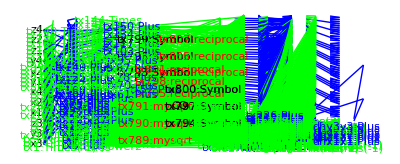

```mathematica
packGraph[chiralRestraintPack]
```

## Cartesian anchor term. Anchor atoms at a specific position with a harmonic potential - Expand the gradient and Hessian.

```mathematica
Clear[x1,y1,z1,x2,y2,z2,ka];
```

```mathematica
bx = { x1, y1, z1};
ba = { xa, ya, za };
```

```mathematica
anchorDeviation = (bx-ba).(bx-ba);
```

```mathematica
anchorEnergyFn =  ka  (anchorDeviation)
```

ka ((x1-xa)^2+(y1-ya)^2+(z1-za)^2)

```mathematica
names = Flatten[{bx}]
```

{x1,y1,z1}

### Energy function

```mathematica
anchorVarNames = { 
{x1,x,I1,0},
{y1,y,I1,1},
{z1,z,I1,2}
};
```

```mathematica
anchorSetupRules = {};
AppendTo[anchorSetupRules,CCode["ANCHOR_RESTRAINT_SET_PARAMETER(ka);"]];
AppendTo[anchorSetupRules,CCode["ANCHOR_RESTRAINT_SET_PARAMETER(xa);"]];
AppendTo[anchorSetupRules,CCode["ANCHOR_RESTRAINT_SET_PARAMETER(ya);"]];
AppendTo[anchorSetupRules,CCode["ANCHOR_RESTRAINT_SET_PARAMETER(za);"]];AppendTo[anchorSetupRules,CCode["ANCHOR_RESTRAINT_SET_PARAMETER(I1);"]];
```

```mathematica
For[i=1,i≤Length[anchorVarNames],i++,
str = "ANCHOR_RESTRAINT_SET_POSITION("<>ToString[anchorVarNames[[i]][[1]]]<>","<>ToString[anchorVarNames[[i]][[3]]]<>","<>ToString[anchorVarNames[[i]][[4]]]<>");";
Print[str];
AppendTo[anchorSetupRules,CCode[str]];
];
```

ANCHOR_RESTRAINT_SET_POSITION(x1,I1,0);

ANCHOR_RESTRAINT_SET_POSITION(y1,I1,1);

ANCHOR_RESTRAINT_SET_POSITION(z1,I1,2);

```mathematica
anchorSetupRules//MatrixForm
```

(CCode[ANCHOR_RESTRAINT_SET_PARAMETER(ka);]
CCode[ANCHOR_RESTRAINT_SET_PARAMETER(xa);]
CCode[ANCHOR_RESTRAINT_SET_PARAMETER(ya);]
CCode[ANCHOR_RESTRAINT_SET_PARAMETER(za);]
CCode[ANCHOR_RESTRAINT_SET_PARAMETER(I1);]
CCode[ANCHOR_RESTRAINT_SET_POSITION(x1,I1,0);]
CCode[ANCHOR_RESTRAINT_SET_POSITION(y1,I1,1);]
CCode[ANCHOR_RESTRAINT_SET_POSITION(z1,I1,2);])

```mathematica
anchorEnergyRules = {};
anchorOutputs = {};
AppendTo[anchorEnergyRules,Assign[AnchorDeviation,anchorDeviation]];
AppendTo[anchorEnergyRules,Assign[Energy,anchorEnergyFn]];
AppendTo[anchorEnergyRules,EnergyAccumulate["ANCHOR_RESTRAINT",Energy]];
AppendTo[anchorOutputs,Energy];
```

### Gradient and Hessian

```mathematica
anchorEnergyFn
```

ka ((x1-xa)^2+(y1-ya)^2+(z1-za)^2)

```mathematica
(anchorHessian = Table[Table[0,{6}],{6}])//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
anchorForceHessianRules = {};
```

```mathematica
AppendGradientForceAndHessian["ANCHOR_RESTRAINT",anchorForceHessianRules,anchorOutputs,anchorHessian,anchorEnergyFn,anchorVarNames];
```

```mathematica
anchorHessian//MatrixForm
```

(5 | 8 | 9 | 0 | 0 | 0
8 | 6 | 10 | 0 | 0 | 0
9 | 10 | 7 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
anchorOutputs
```

{Energy,fx1,fy1,fz1,dhx1x1,dhy1y1,dhz1z1,ohx1y1,ohx1z1,ohy1z1}

### Collect terms and convert to C code

```mathematica
anchorAllRules ={
anchorSetupRules,
anchorEnergyRules,
anchorForceHessianRules};
```

```mathematica
anchorRules = Flatten[anchorAllRules];
```

```mathematica
anchorRules//MatrixForm
```

(CCode[ANCHOR_RESTRAINT_SET_PARAMETER(ka);]
CCode[ANCHOR_RESTRAINT_SET_PARAMETER(xa);]
CCode[ANCHOR_RESTRAINT_SET_PARAMETER(ya);]
CCode[ANCHOR_RESTRAINT_SET_PARAMETER(za);]
CCode[ANCHOR_RESTRAINT_SET_PARAMETER(I1);]
CCode[ANCHOR_RESTRAINT_SET_POSITION(x1,I1,0);]
CCode[ANCHOR_RESTRAINT_SET_POSITION(y1,I1,1);]
CCode[ANCHOR_RESTRAINT_SET_POSITION(z1,I1,2);]
(x1-xa)^2+(y1-ya)^2+(z1-za)^2→AnchorDeviation
ka ((x1-xa)^2+(y1-ya)^2+(z1-za)^2)→Energy
CCode[ANCHOR_RESTRAINT_ENERGY_ACCUMULATE(Energy);]
CCode[#ifdef ANCHOR_RESTRAINT_CALC_FORCE //[]
CCode[if ( calcForce ) {]
2 ka (x1-xa)→gx1
-gx1→fx1
CCode[ANCHOR_RESTRAINT_FORCE_ACCUMULATE(I1, 0, fx1 );]
2 ka (y1-ya)→gy1
-gy1→fy1
CCode[ANCHOR_RESTRAINT_FORCE_ACCUMULATE(I1, 1, fy1 );]
2 ka (z1-za)→gz1
-gz1→fz1
CCode[ANCHOR_RESTRAINT_FORCE_ACCUMULATE(I1, 2, fz1 );]
CCode[#ifdef ANCHOR_RESTRAINT_CALC_DIAGONAL_HESSIAN //[]
CCode[if ( calcDiagonalHessian ) {]
2 ka→dhx1x1
CCode[ANCHOR_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 0, dhx1x1);]
2 ka→dhy1y1
CCode[ANCHOR_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 1, dhy1y1);]
2 ka→dhz1z1
CCode[ANCHOR_RESTRAINT_DIAGONAL_HESSIAN_ACCUMULATE(I1, 2, I1, 2, dhz1z1);]
CCode[#ifdef ANCHOR_RESTRAINT_CALC_OFF_DIAGONAL_HESSIAN //[]
CCode[if ( calcOffDiagonalHessian ) {]
0→ohx1y1
CCode[ANCHOR_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 1, ohx1y1);]
0→ohx1z1
CCode[ANCHOR_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 0, I1, 2, ohx1z1);]
0→ohy1z1
CCode[ANCHOR_RESTRAINT_OFF_DIAGONAL_HESSIAN_ACCUMULATE(I1, 1, I1, 2, ohy1z1);]
CCode[} /*if calcOffDiagonalHessian */ ]
CCode[#endif /* ANCHOR_RESTRAINT_CALC_OFF_DIAGONAL_HESSIAN ]*/]
CCode[} /*calcDiagonalHessian */]
CCode[#endif /* ANCHOR_RESTRAINT_CALC_DIAGONAL_HESSIAN ]*/]
CCode[} /*calcForce */]
CCode[#endif /* ANCHOR_RESTRAINT_CALC_FORCE ]*/])

```mathematica
anchorInput = {x1,y1,z1,xa,ya,za,ka};
```

```mathematica
AppendTo[anchorOutputs,AnchorDeviation];
```

```mathematica
anchorPack0 = {
Name->"AnchorRestraint",
AdditionalCDeclares->"",
DerivativeVariables->{x1,y1,z1},
HessianStructure->anchorHessian,
Rules->anchorRules,
Input->anchorInput,
Output->anchorOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[anchorPack0];
```

Writing finite difference debug code to: _AnchorRestraint_debugFiniteDifference.cc

Writing debug variable declares to: _AnchorRestraint_debugEvalDeclares.cc

Writing xml output debug code to: _AnchorRestraint_debugEvalSerialize.cc

Writing set variables debug code to: _AnchorRestraint_debugEvalSet.cc

anchorPack = Block[{PrintTemporary = Print}, packOptimize[anchorPack0]];

```mathematica
anchorPack = packOptimize[anchorPack0];
```

Set TimesSimplify and PlusSimplify to turn these simplifications off and on

PlusOptimize = False

TimesOptimize = False

Writing declares to file: _AnchorRestraint_termDeclares.cc

Writing code to file: _AnchorRestraint_termCode.cc

Ignore errors in packGraph[anchorPack], I forget what it doesn't like but it is something non-essential

Part::partw: Part 1 of {} does not exist.

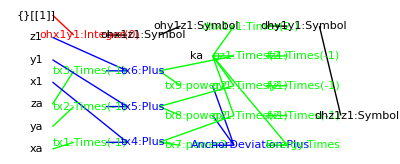

```mathematica
packGraph[anchorPack]
```

## Fixed non-bonding terms - Van der Waals and Electrostatic interactions with atoms that are fixed in space. - Expand the gradient and Hessian in the most straightforward, simple-minded way, don't use the chain rule approach.

```mathematica
Clear[x1,y1,z1,xf,yf,zf, evdw, eeel,fixedNonBondEquation];
```

```mathematica
ba = { x1, y1, z1};
bb = { xf, yf, zf };
```

```mathematica
fixedNonBondInputs = Flatten[{ba,bb,dA,dC,dQ1Q2}]
```

{x1,y1,z1,xf,yf,zf,dA,dC,dQ1Q2}

```mathematica
fixedNonBondDistance = Sqrt[Dot[(ba-bb),(ba-bb)]];
```

```mathematica
efvdwEquation = (dA/fixedNonBondDistance^12-dC/fixedNonBondDistance^6)
```

dA/(((x1-xf)^2+(y1-yf)^2+(z1-zf)^2)^6)-dC/(((x1-xf)^2+(y1-yf)^2+(z1-zf)^2)^3)

```mathematica
efeelEquation = (dQ1Q2/fixedNonBondDistance)
```

dQ1Q2/(√((x1-xf)^2+(y1-yf)^2+(z1-zf)^2))

```mathematica
fixedNonBondEquation = efvdwEquation + efeelEquation
```

dA/(((x1-xf)^2+(y1-yf)^2+(z1-zf)^2)^6)-dC/(((x1-xf)^2+(y1-yf)^2+(z1-zf)^2)^3)+dQ1Q2/(√((x1-xf)^2+(y1-yf)^2+(z1-zf)^2))

```mathematica
names = Flatten[{ba}]
```

{x1,y1,z1}

### Energy

```mathematica
fixedNonBondVarNames = { 
{x1,x,I1,0},
{y1,y,I1,1},
{z1,z,I1,2}
};
```

```mathematica
fixedNonBondSetupRules = {};
AppendTo[fixedNonBondSetupRules,CCode["// FNONBOND_SET_PARAMETER(xf);"]];
AppendTo[fixedNonBondSetupRules,CCode["// FNONBOND_SET_PARAMETER(yf);"]];
AppendTo[fixedNonBondSetupRules,CCode["// FNONBOND_SET_PARAMETER(zf);"]];
AppendTo[fixedNonBondSetupRules,CCode["// FNONBOND_SET_PARAMETER(I1);"]];
AppendTo[fixedNonBondSetupRules,CCode["// FNONBOND_SET_PARAMETER(dQ1Q2);"]];AppendTo[fixedNonBondSetupRules,CCode["// FNONBOND_SET_PARAMETER(dA);"]];
AppendTo[fixedNonBondSetupRules,CCode["// FNONBOND_SET_PARAMETER(dC);"]];
```

```mathematica
For[i=1,i≤Length[fixedNonBondVarNames],i++,
str = "FNONBOND_SET_POSITION("<>ToString[fixedNonBondVarNames[[i]][[1]]]<>","<>ToString[fixedNonBondVarNames[[i]][[3]]]<>","<>ToString[fixedNonBondVarNames[[i]][[4]]]<>");";
Print[str];
AppendTo[fixedNonBondSetupRules,CCode[str]];
];
```

FNONBOND_SET_POSITION(x1,I1,0);

FNONBOND_SET_POSITION(y1,I1,1);

FNONBOND_SET_POSITION(z1,I1,2);

```mathematica
fixedNonBondSetupRules//MatrixForm
```

(CCode[// FNONBOND_SET_PARAMETER(xf);]
CCode[// FNONBOND_SET_PARAMETER(yf);]
CCode[// FNONBOND_SET_PARAMETER(zf);]
CCode[// FNONBOND_SET_PARAMETER(I1);]
CCode[// FNONBOND_SET_PARAMETER(dQ1Q2);]
CCode[// FNONBOND_SET_PARAMETER(dA);]
CCode[// FNONBOND_SET_PARAMETER(dC);]
CCode[FNONBOND_SET_POSITION(x1,I1,0);]
CCode[FNONBOND_SET_POSITION(y1,I1,1);]
CCode[FNONBOND_SET_POSITION(z1,I1,2);])

```mathematica
fixedNonBondEnergyRules = {};
fixedNonBondOutputs = {};
AppendTo[fixedNonBondEnergyRules,Assign[NonbondDistance,fixedNonBondDistance]];
AppendTo[fixedNonBondEnergyRules,Assign[Efvdw,efvdwEquation]];
AppendTo[fixedNonBondEnergyRules,EnergyAccumulate["FNONBOND_EFVDW",Efvdw]];
AppendTo[fixedNonBondEnergyRules,Assign[Efeel,efeelEquation]];
AppendTo[fixedNonBondEnergyRules,EnergyAccumulate["FNONBOND_EFEEL",Efeel]];
AppendTo[fixedNonBondEnergyRules,Assign[Energy,Efvdw+Efeel]];
AppendTo[fixedNonBondEnergyRules,EnergyAccumulate["FNONBOND",Energy]];
AppendTo[fixedNonBondOutputs,Energy];
AppendTo[fixedNonBondOutputs,Efvdw];
AppendTo[fixedNonBondOutputs,Efeel];
```

```mathematica
fixedNonBondHessian = Table[Table[0,{6}],{6}]
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
fixedNonBondForceHessianRules = {};
```

```mathematica
AppendGradientForceAndHessian["FNONBOND",fixedNonBondForceHessianRules,fixedNonBondOutputs,fixedNonBondHessian,fixedNonBondEquation,fixedNonBondVarNames];
```

### Collect and simplify.

```mathematica
AppendTo[fixedNonBondOutputs,fixedNonbondDistance]
```

{Energy,Efvdw,Efeel,fx1,fy1,fz1,dhx1x1,dhy1y1,dhz1z1,ohx1y1,ohx1z1,ohy1z1,fixedNonbondDistance}

```mathematica
fixedNonBondOutputs//FullForm
```

List[Energy,Efvdw,Efeel,fx1,fy1,fz1,dhx1x1,dhy1y1,dhz1z1,ohx1y1,ohx1z1,ohy1z1,fixedNonbondDistance]

```mathematica
fixedNonBondRules = Flatten[{fixedNonBondSetupRules,fixedNonBondEnergyRules,fixedNonBondForceHessianRules}];
```

```mathematica
fnbPack0 = {
Name->"FixedNonbond",
AdditionalCDeclares->"",
EnergyFunction->fixedNonBondEquation,
DerivativeVariables->{x1,y1,z1},
HessianStructure->fixedNonBondHessian,
Rules->fixedNonBondRules,
Input->fixedNonBondInputs,
Output->fixedNonBondOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[fnbPack0];
```

Writing finite difference debug code to: _FixedNonbond_debugFiniteDifference.cc

Writing debug variable declares to: _FixedNonbond_debugEvalDeclares.cc

Writing xml output debug code to: _FixedNonbond_debugEvalSerialize.cc

Writing set variables debug code to: _FixedNonbond_debugEvalSet.cc

```mathematica
nbPack = packOptimize[fnbPack0];
```

Set TimesSimplify and PlusSimplify to turn these simplifications off and on

PlusOptimize = False

TimesOptimize = False

Writing declares to file: _FixedNonbond_termDeclares.cc

Writing code to file: _FixedNonbond_termCode.cc

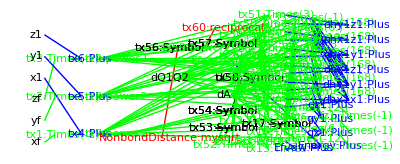

```mathematica
packGraph[nbPack]
```